## First we generate all graphs

We will generate an association containing all graphs.  The key of the graph is computed based on a base 4 representation of the upper half of the “adjacency matrix”.
The matrix itself is tri-valued since 0 means no edge, 1 means and edge and 2 mean they are the same vertex.
For each graph we keep

signature  : the "key"
matrix : the "adjancency matrix"
vertexsets : the "sets " of vertices where contracted vertices are in the same set
vertices : th evertices of the graph
edges : the edges of the graph
graph : a picture of the graph

```mathematica
baseGraphs5=GenAll[5];Length[baseGraphs5]
```

1895

## Now we calculate the relations

We calculate the relations between the graphs.  This is based on the deletion contraction rule.  It links 5 graphs together in a a=b+c relation (or a subtraction)

```mathematica
withRelations5=CompleteRelations[baseGraphs5];Length[withRelations5]
```

1895

For each graph we now add

links  : ids of graphs that are  linked to this graph
relations : a set of equations that involve the current graph.  This set can be empty.  The graph can be mentioned in the relations section of another graph

## Impose a colofour value for the 15 base graphs and propagate this to the others

```mathematica
Table[Labeled[withRelations5[k,"graph"],k],{k,Take[Keys[withRelations5],20]}]
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-9,-Graphics-10,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-16,-Graphics-18,-Graphics-22,-Graphics-26,-Graphics-27,-Graphics-28,-Graphics-30,-Graphics-31,-Graphics-36}

```mathematica
{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-9,-Graphics-10,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-15,-Graphics-18,-Graphics-22,-Graphics-25,-Graphics-27,-Graphics-28,-Graphics-30,-Graphics-31,-Graphics-35}
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-5,-Graphics-9,-Graphics-10,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-15,-Graphics-18,-Graphics-22,-Graphics-25,-Graphics-27,-Graphics-28,-Graphics-30,-Graphics-31,-Graphics-35}

We take a list of graphs as defined in https://en.wikipedia.org/wiki/Bell_number and give them an arbitrary value.

```mathematica
completeGraphs5=Select[Reverse[Keys[withRelations5]],CompleteGraphQ[withRelations5[#,"graph"]]&];Length[completeGraphs5]
```

52

```mathematica
baseGraphAxioma5=Block[{start=0},Table[start++;Symbol["x"<>ToString[k]]->PartitionToSymbol[withRelations5[k,"vertexsets"]],{k,completeGraphs5}]]
```

{x59048→v12345,x58288→v1234x5,x56770→v1235x4,x56012→v123x45,x56011→v123x4x5,x52232→v1245x3,x51478→v124x35,x51475→v124x3x5,x49972→v125x34,x49963→v125x3x4,x49220→v12x345,x49216→v12x34x5,x49210→v12x35x4,x49208→v12x3x45,x49207→v12x3x4x5,x39014→v1345x2,x38308→v134x25,x38281→v134x2x5,x36898→v135x24,x36817→v135x2x4,x36194→v13x245,x36166→v13x24x5,x36112→v13x25x4,x36086→v13x2x45,x36085→v13x2x4x5,x32684→v145x23,x32441→v145x2x3,x31984→v14x235,x31954→v14x23x5,x31738→v14x25x3,x31714→v14x2x35,x31711→v14x2x3x5,x30586→v15x234,x30496→v15x23x4,x30334→v15x24x3,x30262→v15x2x34,x30253→v15x2x3x4,x29888→v1x2345,x29857→v1x234x5,x29797→v1x235x4,x29768→v1x23x45,x29767→v1x23x4x5,x29633→v1x245x3,x29608→v1x24x35,x29605→v1x24x3x5,x29560→v1x25x34,x29551→v1x25x3x4,x29537→v1x2x345,x29533→v1x2x34x5,x29527→v1x2x35x4,x29525→v1x2x3x45,x29524→v1x2x3x4x5}

Now we get some lists of variables

```mathematica
allGraphVariables5=Table[Symbol["x"<> ToString[key]],{key,Keys[withRelations5]}];Length[allGraphVariables5]
```

1895

```mathematica
baseGraphAxioma5Vars=Sort[DeleteDuplicates[Flatten[Map[getAllVariables[#[[2]]]&,baseGraphAxioma5]]]];Length[baseGraphAxioma5Vars]
```

52

```mathematica
baseKeys5=Map[SymbolToKey[#[[1]]]&,baseGraphAxioma5]
```

{59048,58288,56770,56012,56011,52232,51478,51475,49972,49963,49220,49216,49210,49208,49207,39014,38308,38281,36898,36817,36194,36166,36112,36086,36085,32684,32441,31984,31954,31738,31714,31711,30586,30496,30334,30262,30253,29888,29857,29797,29768,29767,29633,29608,29605,29560,29551,29537,29533,29527,29525,29524}

```mathematica
Take[baseGraphAxioma5Vars,5]
```

{v12345,v1234x5,v1235x4,v123x45,v123x4x5}

```mathematica
{v123455,v12345x5,v12345x5,v1234x55,v1234x5x5}
```

{v123455,v12345x5,v12345x5,v1234x55,v1234x5x5}

We now take all relations.  Then we combined this with the base graph axioms.  This gives a huge expression list of 7507 equations

We are now in a position to assign the first colofour to each graph:

```mathematica
Monitor[Table[
withRelations5[key]["colofour"]=Simplify[Symbol["x"<>ToString[key]]/.baseGraphAxioma5],
{key,baseKeys5}
],key];
```

## Calculate the colortables

First we create the colortables, inventing variables on the fly if we need them.  Then we solve these variables and discover that once again we can get away with only the 52 base variables.
This procedure only works fior the b01... variables since we need 5 vertices for the current implementation

```mathematica
withColorTables5=withRelations5;
```

```mathematica
GenerateColorTable5[assocs_,key_]:=Block[
{mat=assocs[key]["matrix"], comb, colofour=assocs[key]["colofour"],newsym,value},

comb=Subsets[Range[5],{2}];
Table[
value=mat[[c[[1]],c[[2]]]];
If[value==2,
{colofour,0},
If[value==1,
{0,colofour},
newsym=Symbol["x"<>ToString[key]<>"y"<>ToString[c[[1]]]<>"z"<>ToString[c[[2]]]];
{newsym,colofour-newsym}
]
]
,{c,comb}
]
]
```

Example of one color table:

```mathematica
GenerateColorTable5[withColorTables5,2]
```

{{x2y1z2,-x2y1z2+Missing[KeyAbsent,colofour]},{x2y1z3,-x2y1z3+Missing[KeyAbsent,colofour]},{x2y1z4,-x2y1z4+Missing[KeyAbsent,colofour]},{x2y1z5,-x2y1z5+Missing[KeyAbsent,colofour]},{x2y2z3,-x2y2z3+Missing[KeyAbsent,colofour]},{x2y2z4,-x2y2z4+Missing[KeyAbsent,colofour]},{x2y2z5,-x2y2z5+Missing[KeyAbsent,colofour]},{x2y3z4,-x2y3z4+Missing[KeyAbsent,colofour]},{x2y3z5,-x2y3z5+Missing[KeyAbsent,colofour]},{Missing[KeyAbsent,colofour],0}}

First assign a basic colortable to each base graph

```mathematica
baseGraphKeys5=baseKeys5;
```

```mathematica
baseGraphAxioma5Vars
```

{v12345,v1234x5,v1235x4,v123x45,v123x4x5,v1245x3,v124x35,v124x3x5,v125x34,v125x3x4,v12x345,v12x34x5,v12x35x4,v12x3x45,v12x3x4x5,v1345x2,v134x25,v134x2x5,v135x24,v135x2x4,v13x245,v13x24x5,v13x25x4,v13x2x45,v13x2x4x5,v145x23,v145x2x3,v14x235,v14x23x5,v14x25x3,v14x2x35,v14x2x3x5,v15x234,v15x23x4,v15x24x3,v15x2x34,v15x2x3x4,v1x2345,v1x234x5,v1x235x4,v1x23x45,v1x23x4x5,v1x245x3,v1x24x35,v1x24x3x5,v1x25x34,v1x25x3x4,v1x2x345,v1x2x34x5,v1x2x35x4,v1x2x3x45,v1x2x3x4x5}

```mathematica
Monitor[Table[
withColorTables5[k]["colortable"]=GenerateColorTable5[withColorTables5,k]
,
{k,baseGraphKeys5}
],k];
```

```mathematica
Keys[withColorTables5[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links}

```mathematica
NoPrint[p__]:=TrueQ
```

Now we assign the other colortables by making sure their colofour formula is interpreted with the based color tables

```mathematica
TryComputeColourTable5[k_]:=Block[{result=Null,simp,left,r1,r2, done,current},
current=withColorTables5[k];
If[KeyExistsQ[current,"colortable"],
result=withColorTables5[k,"colortable"],
done=False;
Table[
If[!done,
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
If[!KeyExistsQ[withColorTables5[r1],"colortable"],
withColorTables5[r1,"colortable"]=TryComputeColourTable5[r1],
];
If[!KeyExistsQ[withColorTables5[r2],"colortable"],
withColorTables5[r2,"colortable"]=TryComputeColourTable5[r2],

];
withColorTables5[k,"colortable"]=withColorTables5[r1,"colortable"]+withColorTables5[r2,"colortable"];
withColorTables5[k,"colofour"]=withColorTables5[r1,"colofour"]+withColorTables5[r2,"colofour"];
done=False
];
],
]
,{r,withColorTables5[k]["relations"]}
]
];
withColorTables5[k,"colortable"]
]
```

```mathematica
KeyExistsQ[withColorTables5[0],"colortable"]
```

False

```mathematica
TryComputeColourTable5[0];
```

Now collect all relation equations.  There are quite a few of them.

0

```mathematica
Monitor[Table[
withColorTables5[k]["colortable2"]=withColorTables5[k]["colortable"]
,
{k,Keys[withColorTables5]}
],k];
```

## Set “comp” and “compwhy” for graphs that can be embedded and are planar

```mathematica
withComp5=withColorTables5;
```

Start will all graphs GreaterEqual

```mathematica
Table[withComp5[k,"comp"]=GreaterEqual;withComp5[k,"compwhy"]="No IH";k,{k,Keys[withComp5]}]//Length
```

1895

```mathematica
CosyPrint5[key_,assoc_:withComp5, colofour_:"colofour"]:=With[
{current=assoc[key]},
Framed[
Labeled[
Graph[current["graph"],ImageSize->{100,100}],
{Style[
{If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current[colofour]],
current["signature"]
],ChromaticPolynomial[current["graph"],4]/24},ColourForKey[assoc,key]],
current["compwhy"]
},

{Bottom,Top}]]
]
```

```mathematica
ColofourPrint5[key_]:=With[
{current=withComp5[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{70,70}]
}
],
{Style[current["signature"],First[Select[{{"Equal",Blue},{"GreaterEqual",Red},{"Greater",Darker[Green]}},#[[1]]==ToString[current["comp"]]&]]]->TraditionalForm[current["colofour"]],ChromaticPolynomial[current["graph"],4]/24}]]]
```

```mathematica
MayBeReassign[key_,current_,left_,right_]:=Block[
{currentS=ToString[current],
leftS=ToString[left],
rightS=ToString[right],
 result=current},
(*Print[currentS,"  ", leftS, "  ", rightS];*)
If[currentS=="GreaterEqual",
If[leftS=="Greater"||rightS=="Greater",
result=Greater;
]
];
result
]
```

```mathematica
RecalculateComp5[k_,depth_,maxdepth_]:=Block[{result=Null,simp,left,r1,r2, current,newValue},
current=withComp5[k];
If[depth<maxdepth && ! current["marked"],
withComp5[k,"marked"]=True;
markCount++;
Table[
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];


withComp5[r1,"parents"]=Append[withComp5[r1,"parents"],k];
withComp5[r2,"parents"]=Append[withComp5[r2,"parents"],k];
withComp5[k,"children"]=Append[withComp5[k,"children"],{r1,r2}];

RecalculateComp5[r1,depth+1,maxdepth];
RecalculateComp5[r2,depth+1,maxdepth];
newValue=MayBeReassign[k,withComp5[k,"comp"], withComp5[r1,"comp"],withComp5[r2,"comp"]];
If[ToString[withComp5[k,"comp"]]≠ToString[newValue],
Print[k," becomes ", newValue];
withComp5[k,"comp"]=newValue;
withComp5[k,"compwhy"]= "Since " <> ToString[r]<> " and " <> ToString[r1]<> " is " <>  ToString[withComp5[r1,"comp"]] <> " and " <> ToString[r2]<> " is " <>  ToString[withComp5[r2,"comp"]]
];
];
]
,{r,withComp5[k]["relations"]}
];
];withComp5[k,"comp"]
]
```

```mathematica
Table[withComp5[k,"marked"]=False;withComp5[k,"parents"]={};withComp5[k,"children"]={};k,{k,Keys[withComp5]}];markCount=0
```

0

```mathematica
IsPlanarSet[set_,total_]:=Block[{result,sot=set-1,breaks=0,i,previous},
If[Length[set]==1,
result=True,
For[i=2,i≤Length[sot],i++,
If[Mod[sot[[i-1]]+1,total]≠Mod[sot[[i]],total],
breaks++;
]
];
If[Mod[sot[[Length[sot]]]+1,total]≠Mod[sot[[1]],total],
breaks++;
];
result=breaks<2;
];
result
]
```

```mathematica
IsPlanarContraction[assoc_,key_]:=Block[{total},
total=Length[Flatten[assoc[key,"vertexsets"]]];
Fold[And,Table[IsPlanarSet[s,total],{s,assoc[key,"vertexsets"]}]]
];
```

```mathematica
Monitor[Table[If[
MyPlanar[withComp5,k],
withComp5[k,"comp"]=Greater;
withComp5[k,"compwhy"]="Planar contraction";
1,
0]
,{k,baseKeys5}],k]
```

{1,1,1,1,1,1,0,0,1,1,1,1,0,1,0,1,0,1,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1,1,0,1,0,1,1,0,1,1,0,0,0,0,0,1,1,0,0,0}

```mathematica
Table[withComp5[k,"comp"]=Equal;withComp5[k,"compwhy"]="Contains K Five";k,{k,Select[baseKeys5,!PlanarGraphQ[withComp5[#,"graph"]]&]}]//Length
```

1

```mathematica
15
```

15

```mathematica
(*Monitor[
Table[If[
PlanarGraphQ[EmbedGraph5[withComp5,key]],
Print[key, " is planar and follows IH "];
withComp5[key]["compwhy"]="Embedding is planar and follows IH (Plantri 10000)";
withComp5[key]["comp"]=Greater;
1,
0
],{key,Keys[withComp5]}],
key]//Total*)
```

```mathematica
markCount=0
```

0

```mathematica
Monitor[RecalculateComp5[0,0,20],markCount]
```

29529 becomes Greater

29511 becomes Greater

29514 becomes Greater

29515 becomes Greater

29517 becomes Greater

29512 becomes Greater

29513 becomes Greater

29484 becomes Greater

29502 becomes Greater

29506 becomes Greater

29487 becomes Greater

29488 becomes Greater

29485 becomes Greater

29403 becomes Greater

29430 becomes Greater

29433 becomes Greater

29434 becomes Greater

29436 becomes Greater

29431 becomes Greater

29406 becomes Greater

29407 becomes Greater

29404 becomes Greater

29405 becomes Greater

29737 becomes Greater

29647 becomes Greater

29677 becomes Greater

29648 becomes Greater

29646 becomes Greater

29736 becomes Greater

29766 becomes Greater

29826 becomes Greater

29676 becomes Greater

29706 becomes Greater

29160 becomes Greater

29241 becomes Greater

29268 becomes Greater

29277 becomes Greater

29280 becomes Greater

29281 becomes Greater

29282 becomes Greater

29278 becomes Greater

29271 becomes Greater

29272 becomes Greater

29269 becomes Greater

29270 becomes Greater

29250 becomes Greater

29253 becomes Greater

29254 becomes Greater

29251 becomes Greater

29244 becomes Greater

29245 becomes Greater

29247 becomes Greater

29242 becomes Greater

29325 becomes Greater

29353 becomes Greater

29328 becomes Greater

29322 becomes Greater

29350 becomes Greater

29378 becomes Greater

29187 becomes Greater

29196 becomes Greater

29199 becomes Greater

29200 becomes Greater

29197 becomes Greater

29205 becomes Greater

29209 becomes Greater

29190 becomes Greater

29191 becomes Greater

29188 becomes Greater

29232 becomes Greater

29214 becomes Greater

29169 becomes Greater

29172 becomes Greater

29173 becomes Greater

29174 becomes Greater

29170 becomes Greater

29178 becomes Greater

29182 becomes Greater

29186 becomes Greater

29163 becomes Greater

29164 becomes Greater

29166 becomes Greater

29161 becomes Greater

29162 becomes Greater

30244 becomes Greater

30163 becomes Greater

30406 becomes Greater

29920 becomes Greater

30001 becomes Greater

30010 becomes Greater

30082 becomes Greater

29929 becomes Greater

29938 becomes Greater

28431 becomes Greater

28674 becomes Greater

28755 becomes Greater

28782 becomes Greater

28800 becomes Greater

28804 becomes Greater

28785 becomes Greater

28786 becomes Greater

28783 becomes Greater

28773 becomes Greater

28777 becomes Greater

28758 becomes Greater

28759 becomes Greater

28756 becomes Greater

28701 becomes Greater

28704 becomes Greater

28705 becomes Greater

28702 becomes Greater

28677 becomes Greater

28678 becomes Greater

28675 becomes Greater

28917 becomes Greater

28918 becomes Greater

29008 becomes Greater

29038 becomes Greater

29128 becomes Greater

28948 becomes Greater

29007 becomes Greater

29037 becomes Greater

29097 becomes Greater

28947 becomes Greater

28512 becomes Greater

28539 becomes Greater

28548 becomes Greater

28551 becomes Greater

28552 becomes Greater

28549 becomes Greater

28542 becomes Greater

28543 becomes Greater

28540 becomes Greater

28521 becomes Greater

28524 becomes Greater

28525 becomes Greater

28522 becomes Greater

28515 becomes Greater

28516 becomes Greater

28513 becomes Greater

28593 becomes Greater

28596 becomes Greater

28624 becomes Greater

28621 becomes Greater

28458 becomes Greater

28467 becomes Greater

28470 becomes Greater

28471 becomes Greater

28468 becomes Greater

28476 becomes Greater

28480 becomes Greater

28461 becomes Greater

28462 becomes Greater

28459 becomes Greater

28440 becomes Greater

28443 becomes Greater

28444 becomes Greater

28441 becomes Greater

28449 becomes Greater

28453 becomes Greater

28434 becomes Greater

28435 becomes Greater

28432 becomes Greater

30981 becomes Greater

30978 becomes Greater

30951 becomes Greater

30954 becomes Greater

31924 becomes Greater

31194 becomes Greater

31224 becomes Greater

30708 becomes Greater

30735 becomes Greater

30738 becomes Greater

31468 becomes Greater

32198 becomes Greater

31465 becomes Greater

30711 becomes Greater

31441 becomes Greater

31438 becomes Greater

26244 becomes Greater

26973 becomes Greater

27216 becomes Greater

27297 becomes Greater

27324 becomes Greater

27327 becomes Greater

27328 becomes Greater

27330 becomes Greater

27325 becomes Greater

27300 becomes Greater

27301 becomes Greater

27298 becomes Greater

27243 becomes Greater

27246 becomes Greater

27247 becomes Greater

27249 becomes Greater

27244 becomes Greater

27219 becomes Greater

27220 becomes Greater

27217 becomes Greater

27459 becomes Greater

27460 becomes Greater

27550 becomes Greater

27580 becomes Greater

27490 becomes Greater

27549 becomes Greater

27579 becomes Greater

27489 becomes Greater

27519 becomes Greater

27054 becomes Greater

27081 becomes Greater

27090 becomes Greater

27093 becomes Greater

27094 becomes Greater

27091 becomes Greater

27084 becomes Greater

27085 becomes Greater

27082 becomes Greater

27063 becomes Greater

27066 becomes Greater

27067 becomes Greater

27064 becomes Greater

27057 becomes Greater

27058 becomes Greater

27060 becomes Greater

27055 becomes Greater

27000 becomes Greater

27009 becomes Greater

27012 becomes Greater

27013 becomes Greater

27010 becomes Greater

27003 becomes Greater

27004 becomes Greater

27001 becomes Greater

27027 becomes Greater

26982 becomes Greater

26985 becomes Greater

26986 becomes Greater

26983 becomes Greater

26976 becomes Greater

26977 becomes Greater

26979 becomes Greater

26974 becomes Greater

28065 becomes Greater

28056 becomes Greater

27975 becomes Greater

27984 becomes Greater

28218 becomes Greater

28308 becomes Greater

27732 becomes Greater

27813 becomes Greater

27822 becomes Greater

27741 becomes Greater

26487 becomes Greater

26568 becomes Greater

26595 becomes Greater

26604 becomes Greater

26607 becomes Greater

26609 becomes Greater

26598 becomes Greater

26599 becomes Greater

26596 becomes Greater

26597 becomes Greater

26577 becomes Greater

26580 becomes Greater

26571 becomes Greater

26572 becomes Greater

26569 becomes Greater

26514 becomes Greater

26523 becomes Greater

26526 becomes Greater

26517 becomes Greater

26518 becomes Greater

26515 becomes Greater

26496 becomes Greater

26499 becomes Greater

26501 becomes Greater

26490 becomes Greater

26491 becomes Greater

26488 becomes Greater

26489 becomes Greater

26730 becomes Greater

26731 becomes Greater

26821 becomes Greater

26851 becomes Greater

26761 becomes Greater

26732 becomes Greater

26852 becomes Greater

26820 becomes Greater

26850 becomes Greater

26760 becomes Greater

26325 becomes Greater

26352 becomes Greater

26361 becomes Greater

26364 becomes Greater

26365 becomes Greater

26366 becomes Greater

26362 becomes Greater

26355 becomes Greater

26356 becomes Greater

26353 becomes Greater

26354 becomes Greater

26334 becomes Greater

26337 becomes Greater

26338 becomes Greater

26335 becomes Greater

26328 becomes Greater

26329 becomes Greater

26326 becomes Greater

26271 becomes Greater

26280 becomes Greater

26283 becomes Greater

26284 becomes Greater

26281 becomes Greater

26274 becomes Greater

26275 becomes Greater

26272 becomes Greater

26253 becomes Greater

26256 becomes Greater

26257 becomes Greater

26258 becomes Greater

26254 becomes Greater

26247 becomes Greater

26248 becomes Greater

26245 becomes Greater

26246 becomes Greater

33157 becomes Greater

33889 becomes Greater

33158 becomes Greater

33156 becomes Greater

37548 becomes Greater

33888 becomes Greater

34620 becomes Greater

33129 becomes Greater

33130 becomes Greater

38254 becomes Greater

33862 becomes Greater

37521 becomes Greater

33861 becomes Greater

33048 becomes Greater

33075 becomes Greater

33076 becomes Greater

33808 becomes Greater

33807 becomes Greater

34539 becomes Greater

33049 becomes Greater

33781 becomes Greater

33050 becomes Greater

33780 becomes Greater

19683 becomes Greater

21870 becomes Greater

22599 becomes Greater

22842 becomes Greater

22923 becomes Greater

22950 becomes Greater

22953 becomes Greater

22954 becomes Greater

22951 becomes Greater

22952 becomes Greater

22926 becomes Greater

22927 becomes Greater

22924 becomes Greater

22869 becomes Greater

22872 becomes Greater

22873 becomes Greater

22870 becomes Greater

22845 becomes Greater

22846 becomes Greater

22843 becomes Greater

22844 becomes Greater

22680 becomes Greater

22707 becomes Greater

22716 becomes Greater

22719 becomes Greater

22720 becomes Greater

22721 becomes Greater

22717 becomes Greater

22710 becomes Greater

22711 becomes Greater

22708 becomes Greater

22709 becomes Greater

22689 becomes Greater

22692 becomes Greater

22693 becomes Greater

22690 becomes Greater

22683 becomes Greater

22684 becomes Greater

22681 becomes Greater

22761 becomes Greater

22764 becomes Greater

22792 becomes Greater

22789 becomes Greater

22817 becomes Greater

22626 becomes Greater

22635 becomes Greater

22638 becomes Greater

22639 becomes Greater

22636 becomes Greater

22629 becomes Greater

22630 becomes Greater

22627 becomes Greater

22653 becomes Greater

22608 becomes Greater

22611 becomes Greater

22612 becomes Greater

22613 becomes Greater

22609 becomes Greater

22602 becomes Greater

22603 becomes Greater

22600 becomes Greater

22601 becomes Greater

23680 becomes Greater

23599 becomes Greater

23356 becomes Greater

23437 becomes Greater

23446 becomes Greater

23518 becomes Greater

23365 becomes Greater

22113 becomes Greater

22194 becomes Greater

22221 becomes Greater

22224 becomes Greater

22225 becomes Greater

22227 becomes Greater

22222 becomes Greater

22197 becomes Greater

22198 becomes Greater

22195 becomes Greater

22140 becomes Greater

22143 becomes Greater

22144 becomes Greater

22146 becomes Greater

22141 becomes Greater

22116 becomes Greater

22117 becomes Greater

22114 becomes Greater

21951 becomes Greater

21978 becomes Greater

21987 becomes Greater

21990 becomes Greater

21991 becomes Greater

21988 becomes Greater

21981 becomes Greater

21982 becomes Greater

21979 becomes Greater

21960 becomes Greater

21963 becomes Greater

21964 becomes Greater

21961 becomes Greater

21954 becomes Greater

21955 becomes Greater

21957 becomes Greater

21952 becomes Greater

22032 becomes Greater

22035 becomes Greater

22063 becomes Greater

22038 becomes Greater

22060 becomes Greater

21897 becomes Greater

21906 becomes Greater

21909 becomes Greater

21910 becomes Greater

21907 becomes Greater

21900 becomes Greater

21901 becomes Greater

21898 becomes Greater

21879 becomes Greater

21882 becomes Greater

21883 becomes Greater

21880 becomes Greater

21873 becomes Greater

21874 becomes Greater

21876 becomes Greater

21871 becomes Greater

24411 becomes Greater

25141 becomes Greater

24414 becomes Greater

24408 becomes Greater

25138 becomes Greater

25868 becomes Greater

24381 becomes Greater

24384 becomes Greater

25114 becomes Greater

25111 becomes Greater

24138 becomes Greater

24165 becomes Greater

24168 becomes Greater

24898 becomes Greater

24895 becomes Greater

25625 becomes Greater

24141 becomes Greater

24871 becomes Greater

24144 becomes Greater

24868 becomes Greater

20412 becomes Greater

20655 becomes Greater

20736 becomes Greater

20763 becomes Greater

20781 becomes Greater

20785 becomes Greater

20766 becomes Greater

20767 becomes Greater

20764 becomes Greater

20754 becomes Greater

20758 becomes Greater

20739 becomes Greater

20740 becomes Greater

20737 becomes Greater

20682 becomes Greater

20685 becomes Greater

20686 becomes Greater

20683 becomes Greater

20658 becomes Greater

20659 becomes Greater

20656 becomes Greater

20493 becomes Greater

20520 becomes Greater

20529 becomes Greater

20532 becomes Greater

20533 becomes Greater

20530 becomes Greater

20523 becomes Greater

20524 becomes Greater

20521 becomes Greater

20502 becomes Greater

20505 becomes Greater

20506 becomes Greater

20503 becomes Greater

20496 becomes Greater

20497 becomes Greater

20494 becomes Greater

20439 becomes Greater

20448 becomes Greater

20451 becomes Greater

20452 becomes Greater

20449 becomes Greater

20457 becomes Greater

20461 becomes Greater

20442 becomes Greater

20443 becomes Greater

20440 becomes Greater

20466 becomes Greater

20484 becomes Greater

20421 becomes Greater

20424 becomes Greater

20425 becomes Greater

20422 becomes Greater

20430 becomes Greater

20434 becomes Greater

20415 becomes Greater

20416 becomes Greater

20413 becomes Greater

21501 becomes Greater

21510 becomes Greater

21492 becomes Greater

21411 becomes Greater

21420 becomes Greater

21168 becomes Greater

21249 becomes Greater

21258 becomes Greater

21177 becomes Greater

21186 becomes Greater

19926 becomes Greater

20007 becomes Greater

20034 becomes Greater

20043 becomes Greater

20046 becomes Greater

20048 becomes Greater

20052 becomes Greater

20056 becomes Greater

20060 becomes Greater

20037 becomes Greater

20038 becomes Greater

20040 becomes Greater

20035 becomes Greater

20036 becomes Greater

20016 becomes Greater

20019 becomes Greater

20025 becomes Greater

20029 becomes Greater

20010 becomes Greater

20011 becomes Greater

20008 becomes Greater

19953 becomes Greater

19962 becomes Greater

19965 becomes Greater

19956 becomes Greater

19957 becomes Greater

19959 becomes Greater

19954 becomes Greater

19935 becomes Greater

19938 becomes Greater

19940 becomes Greater

19929 becomes Greater

19930 becomes Greater

19927 becomes Greater

19928 becomes Greater

19764 becomes Greater

19791 becomes Greater

19800 becomes Greater

19803 becomes Greater

19804 becomes Greater

19805 becomes Greater

19801 becomes Greater

19794 becomes Greater

19795 becomes Greater

19792 becomes Greater

19793 becomes Greater

19773 becomes Greater

19776 becomes Greater

19777 becomes Greater

19774 becomes Greater

19767 becomes Greater

19768 becomes Greater

19770 becomes Greater

19765 becomes Greater

19710 becomes Greater

19719 becomes Greater

19722 becomes Greater

19723 becomes Greater

19720 becomes Greater

19728 becomes Greater

19732 becomes Greater

19713 becomes Greater

19714 becomes Greater

19711 becomes Greater

19692 becomes Greater

19695 becomes Greater

19696 becomes Greater

19697 becomes Greater

19693 becomes Greater

19701 becomes Greater

19705 becomes Greater

19709 becomes Greater

19686 becomes Greater

19687 becomes Greater

19689 becomes Greater

19684 becomes Greater

19685 becomes Greater

48451 becomes Greater

46183 becomes Greater

46184 becomes Greater

46182 becomes Greater

48450 becomes Greater

49206 becomes Greater

50718 becomes Greater

46938 becomes Greater

47694 becomes Greater

56010 becomes Greater

39378 becomes Greater

39379 becomes Greater

41647 becomes Greater

42403 becomes Greater

40135 becomes Greater

39380 becomes Greater

42404 becomes Greater

41646 becomes Greater

42402 becomes Greater

40134 becomes Greater

41650 becomes Greater

39382 becomes Greater

39375 becomes Greater

46179 becomes Greater

46180 becomes Greater

48448 becomes Greater

48447 becomes Greater

49203 becomes Greater

50715 becomes Greater

46935 becomes Greater

55252 becomes Greater

55251 becomes Greater

39376 becomes Greater

41644 becomes Greater

42400 becomes Greater

43156 becomes Greater

40132 becomes Greater

41643 becomes Greater

42399 becomes Greater

40131 becomes Greater

40887 becomes Greater

40144 becomes Greater

40140 becomes Greater

49212 becomes Greater

40896 becomes Greater

39384 becomes Greater

39388 becomes Greater

48460 becomes Greater

39392 becomes Greater

48456 becomes Greater

57528 becomes Greater

39366 becomes Greater

39369 becomes Greater

46173 becomes Greater

46174 becomes Greater

48442 becomes Greater

49198 becomes Greater

49954 becomes Greater

46930 becomes Greater

48441 becomes Greater

49197 becomes Greater

46929 becomes Greater

47685 becomes Greater

53734 becomes Greater

53733 becomes Greater

39370 becomes Greater

41638 becomes Greater

42394 becomes Greater

44662 becomes Greater

40126 becomes Greater

41637 becomes Greater

42393 becomes Greater

43905 becomes Greater

40125 becomes Greater

41640 becomes Greater

49200 becomes Greater

43908 becomes Greater

39372 becomes Greater

46932 becomes Greater

54492 becomes Greater

46170 becomes Greater

46171 becomes Greater

48439 becomes Greater

49195 becomes Greater

46927 becomes Greater

46172 becomes Greater

49196 becomes Greater

48438 becomes Greater

49194 becomes Greater

46926 becomes Greater

52975 becomes Greater

52976 becomes Greater

52974 becomes Greater

39367 becomes Greater

41635 becomes Greater

42391 becomes Greater

43147 becomes Greater

44659 becomes Greater

40123 becomes Greater

39368 becomes Greater

42392 becomes Greater

45416 becomes Greater

41634 becomes Greater

42390 becomes Greater

43902 becomes Greater

40122 becomes Greater

40878 becomes Greater

0 becomes Greater

13230 becomes Greater

13231 becomes Greater

15427 becomes Greater

16159 becomes Greater

13963 becomes Greater

13232 becomes Greater

16160 becomes Greater

15426 becomes Greater

16158 becomes Greater

13962 becomes Greater

15454 becomes Greater

13258 becomes Greater

13203 becomes Greater

13204 becomes Greater

15400 becomes Greater

16132 becomes Greater

16864 becomes Greater

13936 becomes Greater

15399 becomes Greater

16131 becomes Greater

13935 becomes Greater

14667 becomes Greater

14044 becomes Greater

14016 becomes Greater

14748 becomes Greater

13284 becomes Greater

13312 becomes Greater

13340 becomes Greater

13122 becomes Greater

13149 becomes Greater

13150 becomes Greater

15346 becomes Greater

16078 becomes Greater

18274 becomes Greater

13882 becomes Greater

15345 becomes Greater

16077 becomes Greater

17541 becomes Greater

13881 becomes Greater

15372 becomes Greater

17568 becomes Greater

13176 becomes Greater

13123 becomes Greater

15319 becomes Greater

16051 becomes Greater

16783 becomes Greater

18247 becomes Greater

13855 becomes Greater

13124 becomes Greater

16052 becomes Greater

18980 becomes Greater

15318 becomes Greater

16050 becomes Greater

17514 becomes Greater

13854 becomes Greater

14586 becomes Greater

6561 becomes Greater

11214 becomes Greater

11217 becomes Greater

11244 becomes Greater

11187 becomes Greater

11190 becomes Greater

12650 becomes Greater

10944 becomes Greater

10971 becomes Greater

10974 becomes Greater

11704 becomes Greater

11701 becomes Greater

10998 becomes Greater

10947 becomes Greater

11677 becomes Greater

12407 becomes Greater

11674 becomes Greater

8748 becomes Greater

10534 becomes Greater

10543 becomes Greater

10552 becomes Greater

10453 becomes Greater

10462 becomes Greater

10210 becomes Greater

10291 becomes Greater

10300 becomes Greater

10219 becomes Greater

10228 becomes Greater

9477 becomes Greater

9720 becomes Greater

9801 becomes Greater

9828 becomes Greater

9837 becomes Greater

9840 becomes Greater

9842 becomes Greater

9846 becomes Greater

9850 becomes Greater

9854 becomes Greater

9831 becomes Greater

9832 becomes Greater

9834 becomes Greater

9829 becomes Greater

9830 becomes Greater

9810 becomes Greater

9813 becomes Greater

9819 becomes Greater

9823 becomes Greater

9804 becomes Greater

9805 becomes Greater

9802 becomes Greater

9747 becomes Greater

9756 becomes Greater

9759 becomes Greater

9750 becomes Greater

9751 becomes Greater

9753 becomes Greater

9748 becomes Greater

9729 becomes Greater

9732 becomes Greater

9734 becomes Greater

9723 becomes Greater

9724 becomes Greater

9721 becomes Greater

9722 becomes Greater

9558 becomes Greater

9585 becomes Greater

9594 becomes Greater

9597 becomes Greater

9598 becomes Greater

9599 becomes Greater

9595 becomes Greater

9588 becomes Greater

9589 becomes Greater

9586 becomes Greater

9587 becomes Greater

9567 becomes Greater

9570 becomes Greater

9571 becomes Greater

9568 becomes Greater

9561 becomes Greater

9562 becomes Greater

9564 becomes Greater

9559 becomes Greater

9504 becomes Greater

9513 becomes Greater

9516 becomes Greater

9517 becomes Greater

9514 becomes Greater

9522 becomes Greater

9526 becomes Greater

9507 becomes Greater

9508 becomes Greater

9505 becomes Greater

9486 becomes Greater

9489 becomes Greater

9490 becomes Greater

9491 becomes Greater

9487 becomes Greater

9495 becomes Greater

9499 becomes Greater

9503 becomes Greater

9480 becomes Greater

9481 becomes Greater

9483 becomes Greater

9478 becomes Greater

9479 becomes Greater

8991 becomes Greater

9072 becomes Greater

9099 becomes Greater

9108 becomes Greater

9111 becomes Greater

9117 becomes Greater

9121 becomes Greater

9102 becomes Greater

9103 becomes Greater

9100 becomes Greater

9130 becomes Greater

9139 becomes Greater

9148 becomes Greater

9081 becomes Greater

9084 becomes Greater

9085 becomes Greater

9082 becomes Greater

9090 becomes Greater

9094 becomes Greater

9075 becomes Greater

9076 becomes Greater

9073 becomes Greater

9018 becomes Greater

9027 becomes Greater

9030 becomes Greater

9021 becomes Greater

9022 becomes Greater

9019 becomes Greater

9048 becomes Greater

9057 becomes Greater

9000 becomes Greater

9003 becomes Greater

9004 becomes Greater

9001 becomes Greater

8994 becomes Greater

8995 becomes Greater

8992 becomes Greater

8829 becomes Greater

8856 becomes Greater

8865 becomes Greater

8868 becomes Greater

8869 becomes Greater

8866 becomes Greater

8859 becomes Greater

8860 becomes Greater

8857 becomes Greater

8884 becomes Greater

8893 becomes Greater

8838 becomes Greater

8841 becomes Greater

8842 becomes Greater

8839 becomes Greater

8832 becomes Greater

8833 becomes Greater

8830 becomes Greater

8775 becomes Greater

8784 becomes Greater

8787 becomes Greater

8788 becomes Greater

8785 becomes Greater

8793 becomes Greater

8797 becomes Greater

8778 becomes Greater

8779 becomes Greater

8776 becomes Greater

8802 becomes Greater

8811 becomes Greater

8820 becomes Greater

8757 becomes Greater

8760 becomes Greater

8761 becomes Greater

8758 becomes Greater

8766 becomes Greater

8770 becomes Greater

8751 becomes Greater

8752 becomes Greater

8749 becomes Greater

7290 becomes Greater

7533 becomes Greater

7614 becomes Greater

7641 becomes Greater

7650 becomes Greater

7653 becomes Greater

7644 becomes Greater

7645 becomes Greater

7647 becomes Greater

7642 becomes Greater

7623 becomes Greater

7626 becomes Greater

7617 becomes Greater

7618 becomes Greater

7615 becomes Greater

7560 becomes Greater

7569 becomes Greater

7572 becomes Greater

7563 becomes Greater

7564 becomes Greater

7566 becomes Greater

7561 becomes Greater

7542 becomes Greater

7545 becomes Greater

7536 becomes Greater

7537 becomes Greater

7534 becomes Greater

7371 becomes Greater

7398 becomes Greater

7407 becomes Greater

7410 becomes Greater

7411 becomes Greater

7408 becomes Greater

7401 becomes Greater

7402 becomes Greater

7399 becomes Greater

7380 becomes Greater

7383 becomes Greater

7384 becomes Greater

7381 becomes Greater

7374 becomes Greater

7375 becomes Greater

7377 becomes Greater

7372 becomes Greater

7452 becomes Greater

7455 becomes Greater

7483 becomes Greater

7458 becomes Greater

7480 becomes Greater

7317 becomes Greater

7326 becomes Greater

7329 becomes Greater

7330 becomes Greater

7327 becomes Greater

7320 becomes Greater

7321 becomes Greater

7318 becomes Greater

7299 becomes Greater

7302 becomes Greater

7303 becomes Greater

7300 becomes Greater

7293 becomes Greater

7294 becomes Greater

7296 becomes Greater

7291 becomes Greater

8346 becomes Greater

8355 becomes Greater

8436 becomes Greater

8265 becomes Greater

8274 becomes Greater

8022 becomes Greater

8103 becomes Greater

8112 becomes Greater

8184 becomes Greater

8031 becomes Greater

6804 becomes Greater

6885 becomes Greater

6912 becomes Greater

6921 becomes Greater

6924 becomes Greater

6926 becomes Greater

6915 becomes Greater

6916 becomes Greater

6913 becomes Greater

6914 becomes Greater

6943 becomes Greater

6952 becomes Greater

6894 becomes Greater

6897 becomes Greater

6898 becomes Greater

6895 becomes Greater

6888 becomes Greater

6889 becomes Greater

6886 becomes Greater

6975 becomes Greater

6978 becomes Greater

7034 becomes Greater

6831 becomes Greater

6840 becomes Greater

6843 becomes Greater

6834 becomes Greater

6835 becomes Greater

6832 becomes Greater

6861 becomes Greater

6870 becomes Greater

6813 becomes Greater

6816 becomes Greater

6817 becomes Greater

6818 becomes Greater

6814 becomes Greater

6807 becomes Greater

6808 becomes Greater

6805 becomes Greater

6806 becomes Greater

6642 becomes Greater

6669 becomes Greater

6678 becomes Greater

6681 becomes Greater

6682 becomes Greater

6683 becomes Greater

6679 becomes Greater

6672 becomes Greater

6673 becomes Greater

6670 becomes Greater

6671 becomes Greater

6697 becomes Greater

6706 becomes Greater

6651 becomes Greater

6654 becomes Greater

6655 becomes Greater

6652 becomes Greater

6645 becomes Greater

6646 becomes Greater

6643 becomes Greater

6723 becomes Greater

6726 becomes Greater

6754 becomes Greater

6751 becomes Greater

6779 becomes Greater

6588 becomes Greater

6597 becomes Greater

6600 becomes Greater

6601 becomes Greater

6598 becomes Greater

6591 becomes Greater

6592 becomes Greater

6589 becomes Greater

6615 becomes Greater

6624 becomes Greater

6570 becomes Greater

6573 becomes Greater

6574 becomes Greater

6575 becomes Greater

6571 becomes Greater

6564 becomes Greater

6565 becomes Greater

6562 becomes Greater

6563 becomes Greater

2187 becomes Greater

2916 becomes Greater

3159 becomes Greater

3240 becomes Greater

3267 becomes Greater

3276 becomes Greater

3279 becomes Greater

3281 becomes Greater

3270 becomes Greater

3271 becomes Greater

3268 becomes Greater

3269 becomes Greater

3249 becomes Greater

3252 becomes Greater

3243 becomes Greater

3244 becomes Greater

3241 becomes Greater

3186 becomes Greater

3195 becomes Greater

3198 becomes Greater

3189 becomes Greater

3190 becomes Greater

3187 becomes Greater

3168 becomes Greater

3171 becomes Greater

3173 becomes Greater

3162 becomes Greater

3163 becomes Greater

3160 becomes Greater

3161 becomes Greater

3402 becomes Greater

3403 becomes Greater

3493 becomes Greater

3523 becomes Greater

3433 becomes Greater

3404 becomes Greater

3524 becomes Greater

3492 becomes Greater

3522 becomes Greater

3432 becomes Greater

2997 becomes Greater

3024 becomes Greater

3033 becomes Greater

3036 becomes Greater

3037 becomes Greater

3038 becomes Greater

3034 becomes Greater

3027 becomes Greater

3028 becomes Greater

3025 becomes Greater

3026 becomes Greater

3006 becomes Greater

3009 becomes Greater

3010 becomes Greater

3007 becomes Greater

3000 becomes Greater

3001 becomes Greater

2998 becomes Greater

2943 becomes Greater

2952 becomes Greater

2955 becomes Greater

2956 becomes Greater

2953 becomes Greater

2946 becomes Greater

2947 becomes Greater

2944 becomes Greater

2925 becomes Greater

2928 becomes Greater

2929 becomes Greater

2930 becomes Greater

2926 becomes Greater

2919 becomes Greater

2920 becomes Greater

2917 becomes Greater

2918 becomes Greater

3970 becomes Greater

3979 becomes Greater

3889 becomes Greater

3898 becomes Greater

4222 becomes Greater

4132 becomes Greater

3646 becomes Greater

3727 becomes Greater

3736 becomes Greater

3655 becomes Greater

2430 becomes Greater

2511 becomes Greater

2538 becomes Greater

2547 becomes Greater

2550 becomes Greater

2541 becomes Greater

2542 becomes Greater

2544 becomes Greater

2539 becomes Greater

2569 becomes Greater

2578 becomes Greater

2520 becomes Greater

2523 becomes Greater

2524 becomes Greater

2521 becomes Greater

2514 becomes Greater

2515 becomes Greater

2512 becomes Greater

2457 becomes Greater

2466 becomes Greater

2469 becomes Greater

2460 becomes Greater

2461 becomes Greater

2463 becomes Greater

2458 becomes Greater

2487 becomes Greater

2496 becomes Greater

2439 becomes Greater

2442 becomes Greater

2443 becomes Greater

2440 becomes Greater

2433 becomes Greater

2434 becomes Greater

2431 becomes Greater

2673 becomes Greater

2674 becomes Greater

2764 becomes Greater

2794 becomes Greater

2824 becomes Greater

2704 becomes Greater

2763 becomes Greater

2793 becomes Greater

2703 becomes Greater

2733 becomes Greater

2268 becomes Greater

2295 becomes Greater

2304 becomes Greater

2307 becomes Greater

2308 becomes Greater

2305 becomes Greater

2298 becomes Greater

2299 becomes Greater

2296 becomes Greater

2323 becomes Greater

2332 becomes Greater

2277 becomes Greater

2280 becomes Greater

2281 becomes Greater

2284 becomes Greater

2278 becomes Greater

2271 becomes Greater

2272 becomes Greater

2274 becomes Greater

2269 becomes Greater

2214 becomes Greater

2223 becomes Greater

2226 becomes Greater

2227 becomes Greater

2224 becomes Greater

2217 becomes Greater

2218 becomes Greater

2215 becomes Greater

2241 becomes Greater

2250 becomes Greater

2196 becomes Greater

2199 becomes Greater

2200 becomes Greater

2203 becomes Greater

2197 becomes Greater

2190 becomes Greater

2191 becomes Greater

2193 becomes Greater

2188 becomes Greater

4644 becomes Greater

4647 becomes Greater

5377 becomes Greater

4650 becomes Greater

5374 becomes Greater

4674 becomes Greater

4617 becomes Greater

4620 becomes Greater

5350 becomes Greater

5347 becomes Greater

6077 becomes Greater

5620 becomes Greater

5590 becomes Greater

6320 becomes Greater

4860 becomes Greater

4890 becomes Greater

4920 becomes Greater

4374 becomes Greater

4401 becomes Greater

4404 becomes Greater

5134 becomes Greater

5131 becomes Greater

4428 becomes Greater

4377 becomes Greater

5107 becomes Greater

4380 becomes Greater

5104 becomes Greater

5834 becomes Greater

1782 becomes Greater

1791 becomes Greater

1800 becomes Greater

1872 becomes Greater

1701 becomes Greater

1710 becomes Greater

1944 becomes Greater

2034 becomes Greater

2124 becomes Greater

1458 becomes Greater

1539 becomes Greater

1548 becomes Greater

1620 becomes Greater

1467 becomes Greater

1476 becomes Greater

729 becomes Greater

1215 becomes Greater

1216 becomes Greater

1306 becomes Greater

1336 becomes Greater

1426 becomes Greater

1246 becomes Greater

1305 becomes Greater

1335 becomes Greater

1395 becomes Greater

1245 becomes Greater

972 becomes Greater

1053 becomes Greater

1080 becomes Greater

1089 becomes Greater

1092 becomes Greater

1098 becomes Greater

1102 becomes Greater

1083 becomes Greater

1084 becomes Greater

1081 becomes Greater

1062 becomes Greater

1065 becomes Greater

1071 becomes Greater

1075 becomes Greater

1056 becomes Greater

1057 becomes Greater

1054 becomes Greater

999 becomes Greater

1008 becomes Greater

1011 becomes Greater

1002 becomes Greater

1003 becomes Greater

1000 becomes Greater

981 becomes Greater

984 becomes Greater

975 becomes Greater

976 becomes Greater

973 becomes Greater

810 becomes Greater

837 becomes Greater

846 becomes Greater

849 becomes Greater

850 becomes Greater

847 becomes Greater

840 becomes Greater

841 becomes Greater

838 becomes Greater

819 becomes Greater

822 becomes Greater

823 becomes Greater

820 becomes Greater

813 becomes Greater

814 becomes Greater

811 becomes Greater

891 becomes Greater

894 becomes Greater

922 becomes Greater

919 becomes Greater

756 becomes Greater

765 becomes Greater

768 becomes Greater

769 becomes Greater

766 becomes Greater

774 becomes Greater

778 becomes Greater

759 becomes Greater

760 becomes Greater

757 becomes Greater

738 becomes Greater

741 becomes Greater

742 becomes Greater

739 becomes Greater

747 becomes Greater

751 becomes Greater

732 becomes Greater

733 becomes Greater

730 becomes Greater

243 becomes Greater

324 becomes Greater

351 becomes Greater

360 becomes Greater

363 becomes Greater

365 becomes Greater

369 becomes Greater

373 becomes Greater

377 becomes Greater

354 becomes Greater

355 becomes Greater

357 becomes Greater

352 becomes Greater

353 becomes Greater

382 becomes Greater

391 becomes Greater

400 becomes Greater

333 becomes Greater

336 becomes Greater

337 becomes Greater

334 becomes Greater

342 becomes Greater

346 becomes Greater

327 becomes Greater

328 becomes Greater

325 becomes Greater

414 becomes Greater

417 becomes Greater

473 becomes Greater

270 becomes Greater

279 becomes Greater

282 becomes Greater

273 becomes Greater

274 becomes Greater

276 becomes Greater

271 becomes Greater

300 becomes Greater

309 becomes Greater

252 becomes Greater

255 becomes Greater

256 becomes Greater

257 becomes Greater

253 becomes Greater

246 becomes Greater

247 becomes Greater

244 becomes Greater

245 becomes Greater

486 becomes Greater

487 becomes Greater

577 becomes Greater

607 becomes Greater

637 becomes Greater

697 becomes Greater

517 becomes Greater

488 becomes Greater

608 becomes Greater

728 becomes Greater

576 becomes Greater

606 becomes Greater

666 becomes Greater

516 becomes Greater

546 becomes Greater

162 becomes Greater

165 becomes Greater

193 becomes Greater

168 becomes Greater

190 becomes Greater

218 becomes Greater

81 becomes Greater

108 becomes Greater

117 becomes Greater

120 becomes Greater

121 becomes Greater

122 becomes Greater

118 becomes Greater

111 becomes Greater

112 becomes Greater

109 becomes Greater

110 becomes Greater

136 becomes Greater

145 becomes Greater

90 becomes Greater

93 becomes Greater

94 becomes Greater

97 becomes Greater

91 becomes Greater

84 becomes Greater

85 becomes Greater

87 becomes Greater

82 becomes Greater

27 becomes Greater

36 becomes Greater

39 becomes Greater

40 becomes Greater

37 becomes Greater

45 becomes Greater

49 becomes Greater

30 becomes Greater

31 becomes Greater

28 becomes Greater

54 becomes Greater

63 becomes Greater

72 becomes Greater

18 becomes Greater

22 becomes Greater

26 becomes Greater

9 becomes Greater

12 becomes Greater

13 becomes Greater

14 becomes Greater

16 becomes Greater

10 becomes Greater

3 becomes Greater

4 becomes Greater

6 becomes Greater

1 becomes Greater

2 becomes Greater

Greater

Now we have a look at some graphs that might have been forgotten:

```mathematica
Monitor[Table[If[
MyPlanar[withComp5,k],
Print[k, " is a planar contraction"];
withComp5[k,"comp"]=Greater;
withComp5[k,"compwhy"]="Planar contraction (late)";
1,
0]
,{k,Select[Keys[withComp5],ToString[withComp5[#,"comp"]]=="GreaterEqual"&]}],k]//Total
```

280 is a planar contraction

283 is a planar contraction

286 is a planar contraction

361 is a planar contraction

442 is a planar contraction

982 is a planar contraction

985 is a planar contraction

1009 is a planar contraction

1012 is a planar contraction

1063 is a planar contraction

1090 is a planar contraction

1143 is a planar contraction

1171 is a planar contraction

2467 is a planar contraction

2548 is a planar contraction

3169 is a planar contraction

3196 is a planar contraction

3250 is a planar contraction

3277 is a planar contraction

6841 is a planar contraction

6844 is a planar contraction

7306 is a planar contraction

7543 is a planar contraction

7546 is a planar contraction

7570 is a planar contraction

7573 is a planar contraction

7576 is a planar contraction

9028 is a planar contraction

9730 is a planar contraction

9757 is a planar contraction

11917 is a planar contraction

11944 is a planar contraction

19699 is a planar contraction

19936 is a planar contraction

19939 is a planar contraction

19963 is a planar contraction

19966 is a planar contraction

19969 is a planar contraction

20017 is a planar contraction

20044 is a planar contraction

20475 is a planar contraction

20548 is a planar contraction

20557 is a planar contraction

20664 is a planar contraction

20665 is a planar contraction

20667 is a planar contraction

20668 is a planar contraction

20691 is a planar contraction

20692 is a planar contraction

20694 is a planar contraction

20695 is a planar contraction

20712 is a planar contraction

20721 is a planar contraction

20745 is a planar contraction

20746 is a planar contraction

20772 is a planar contraction

20773 is a planar contraction

20794 is a planar contraction

20803 is a planar contraction

20812 is a planar contraction

22122 is a planar contraction

22123 is a planar contraction

22149 is a planar contraction

22150 is a planar contraction

22203 is a planar contraction

22204 is a planar contraction

22230 is a planar contraction

22231 is a planar contraction

22284 is a planar contraction

22312 is a planar contraction

22851 is a planar contraction

22852 is a planar contraction

22856 is a planar contraction

22878 is a planar contraction

22879 is a planar contraction

22932 is a planar contraction

22933 is a planar contraction

22959 is a planar contraction

22960 is a planar contraction

22964 is a planar contraction

23013 is a planar contraction

23041 is a planar contraction

23072 is a planar contraction

23608 is a planar contraction

23689 is a planar contraction

23770 is a planar contraction

26497 is a planar contraction

26500 is a planar contraction

26524 is a planar contraction

26527 is a planar contraction

26989 is a planar contraction

27225 is a planar contraction

27226 is a planar contraction

27228 is a planar contraction

27229 is a planar contraction

27252 is a planar contraction

27253 is a planar contraction

27255 is a planar contraction

27256 is a planar contraction

27259 is a planar contraction

27610 is a planar contraction

28683 is a planar contraction

28684 is a planar contraction

28710 is a planar contraction

28711 is a planar contraction

29412 is a planar contraction

29413 is a planar contraction

29417 is a planar contraction

29439 is a planar contraction

29440 is a planar contraction

30172 is a planar contraction

31681 is a planar contraction

31708 is a planar contraction

35244 is a planar contraction

35245 is a planar contraction

35271 is a planar contraction

35272 is a planar contraction

35976 is a planar contraction

35977 is a planar contraction

35978 is a planar contraction

36003 is a planar contraction

36004 is a planar contraction

36736 is a planar contraction

46936 is a planar contraction

46939 is a planar contraction

46942 is a planar contraction

49204 is a planar contraction

51472 is a planar contraction

128

```mathematica
Select[Keys[withComp5],withComp5[#,"comp"]==Greater&]//Length
```

1702

```mathematica
41579
```

41579

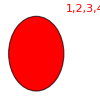
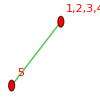
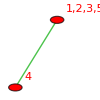
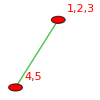
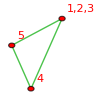
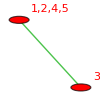
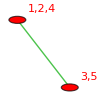
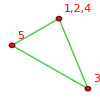
{-Graphics-{59048→v12345,1/6}Planar contraction,-Graphics-{58288→v1234x5,1/2}Planar contraction,-Graphics-{56770→v1235x4,1/2}Planar contraction,-Graphics-{56012→v123x45,1/2}Planar contraction,-Graphics-{56011→v123x4x5,1}Planar contraction,-Graphics-{52232→v1245x3,1/2}Planar contraction,-Graphics-{51478→v124x35,1/2}No IH,-Graphics-{51475→v124x3x5,1}No IH,-Graphics-{49972→v125x34,1/2}Planar contraction,-Graphics-{49963→v125x3x4,1}Planar contraction,-Graphics-{49220→v12x345,1/2}Planar contraction,-Graphics-{49216→v12x34x5,1}Planar contraction,-Graphics-{49210→v12x35x4,1}No IH,-Graphics-{49208→v12x3x45,1}Planar contraction,-Graphics-{49207→v12x3x4x5,1}No IH,-Graphics-{39014→v1345x2,1/2}Planar contraction,-Graphics-{38308→v134x25,1/2}No IH,-Graphics-{38281→v134x2x5,1}Planar contraction,-Graphics-{36898→v135x24,1/2}No IH,-Graphics-{36817→v135x2x4,1}No IH,-Graphics-{36194→v13x245,1/2}No IH,-Graphics-{36166→v13x24x5,1}No IH,-Graphics-{36112→v13x25x4,1}No IH,-Graphics-{36086→v13x2x45,1}No IH,-Graphics-{36085→v13x2x4x5,1}No IH,-Graphics-{32684→v145x23,1/2}Planar contraction,-Graphics-{32441→v145x2x3,1}Planar contraction,-Graphics-{31984→v14x235,1/2}No IH,-Graphics-{31954→v14x23x5,1}Planar contraction,-Graphics-{31738→v14x25x3,1}No IH,-Graphics-{31714→v14x2x35,1}No IH,-Graphics-{31711→v14x2x3x5,1}No IH,-Graphics-{30586→v15x234,1/2}Planar contraction,-Graphics-{30496→v15x23x4,1}Planar contraction,-Graphics-{30334→v15x24x3,1}No IH,-Graphics-{30262→v15x2x34,1}Planar contraction,-Graphics-{30253→v15x2x3x4,1}No IH,-Graphics-{29888→v1x2345,1/2}Planar contraction,-Graphics-{29857→v1x234x5,1}Planar contraction,-Graphics-{29797→v1x235x4,1}No IH,-Graphics-{29768→v1x23x45,1}Planar contraction,-Graphics-{29767→v1x23x4x5,1}Planar contraction,-Graphics-{29633→v1x245x3,1}No IH,-Graphics-{29608→v1x24x35,1}No IH,-Graphics-{29605→v1x24x3x5,1}No IH,-Graphics-{29560→v1x25x34,1}No IH,-Graphics-{29551→v1x25x3x4,1}No IH,-Graphics-{29537→v1x2x345,1}Planar contraction,-Graphics-{29533→v1x2x34x5,1}Planar contraction,-Graphics-{29527→v1x2x35x4,1}No IH,-Graphics-{29525→v1x2x3x45,1}No IH,-Graphics-{29524→v1x2x3x4x5,0}Contains K Five}

```mathematica
Table[CosyPrint5[k,withComp5],{k,baseKeys5}]
```

## We now replace some of the "b" variables with our greek letters

```mathematica
stubbornForm5=withComp5;
```

```mathematica
Keys[stubbornForm5[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,compwhy,marked,parents,children}

```mathematica
stubbornKeys5 = Select[Keys[stubbornForm5],(ToString[stubbornForm5[#]["comp"]]=="GreaterEqual")&];Length[stubbornKeys5]
```

192

```mathematica
Intersection[baseKeys5,stubbornKeys5]//Length
```

26

```mathematica
CosyPrintThree5[key_]:=ColorTablePrint[key,stubbornForm5,"colofour","colortable"]
```

```mathematica
ineqsthree5=Monitor[Table[stubbornForm5[k]["comp"][stubbornForm5[k]["colofour"],0],{k,Keys[stubbornForm5]}],k]//DeleteDuplicates;
```

```mathematica
Length[ineqsthree5]
```

1895

```mathematica
ineqsthree52=Fold[And,ineqsthree5]//Simplify
```

v12345>0&&v1234x5>0&&v1235x4>0&&v123x45>0&&v123x4x5>0&&v1245x3>0&&v124x35≥0&&v124x3x5≥0&&v125x34>0&&v125x3x4>0&&v12x345>0&&v12x34x5>0&&v12x35x4≥0&&v12x3x45>0&&v12x3x4x5≥0&&v1345x2>0&&v134x25≥0&&v134x2x5>0&&v135x24≥0&&v135x2x4≥0&&v13x245≥0&&v13x24x5≥0&&v13x25x4≥0&&v13x2x45≥0&&v13x2x4x5≥0&&v145x23>0&&v145x2x3>0&&v14x235≥0&&v14x23x5>0&&v14x25x3≥0&&v14x2x35≥0&&v14x2x3x5≥0&&v15x234>0&&v15x23x4>0&&v15x24x3≥0&&v15x2x34>0&&v15x2x3x4≥0&&v1x2345>0&&v1x234x5>0&&v1x235x4≥0&&v1x23x45>0&&v1x23x4x5>0&&v1x245x3≥0&&v1x24x35≥0&&v1x24x3x5≥0&&v1x25x34≥0&&v1x25x3x4≥0&&v1x2x345>0&&v1x2x34x5>0&&v1x2x35x4≥0&&v1x2x3x45≥0&&v1x2x3x4x5==0&&v13x25x4+v14x25x3+v1x25x3x4>0&&v134x25+v1x25x34>0&&v13x2x4x5+v1x2x35x4+v1x2x3x4x5>0&&v13x2x45+v1x2x3x45>0&&v13x24x5+v1x24x35+v1x24x3x5>0&&v13x245+v1x245x3>0&&v135x2x4+v15x2x3x4>0&&v135x24+v15x24x3>0&&v14x2x3x5+v1x24x3x5+v1x2x3x4x5>0&&v14x2x35+v1x24x35+v1x2x35x4>0&&v14x235+v1x235x4>0&&v1x245x3+v1x2x3x45>0&&v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5>0&&v15x24x3+v15x2x3x4>0&&v14x2x35+v14x2x3x5>0&&v13x245+v13x2x45>0&&v13x24x5+v13x2x4x5>0&&v135x24+v135x2x4>0&&v124x3x5+v12x3x4x5>0&&v124x35+v12x35x4>0&&v12x35x4+v12x3x4x5>0&&v124x35+v124x3x5>0

```mathematica
ExpressionToTable[ineqsthree52]
```

v15x234>0
v14x235≥0
v13x245≥0
v145x2x3>0
v135x2x4≥0
v134x2x5>0
v1x2x345>0
v1x2345>0
v12x345>0
v12345>0
v1x25x3x4≥0
v15x2x3x4≥0
v15x23x4>0
v125x3x4>0
v1x24x3x5≥0
v14x2x3x5≥0
v124x3x5≥0
v14x23x5>0
v15x24x3≥0
v13x2x4x5≥0
v13x24x5≥0
v12x3x4x5≥0
v1x2x34x5>0
v1x23x4x5>0
v1x234x5>0
v12x34x5>0
v123x4x5>0
v1234x5>0
v1x2x3x4x5==0
v1345x2>0
v1x245x3≥0
v14x25x3≥0
v1245x3>0
v1x2x35x4≥0
v1x235x4≥0
v13x25x4≥0
v12x35x4≥0
v1235x4>0
v145x23>0
v135x24≥0
v134x25≥0
v1x25x34≥0
v15x2x34>0
v125x34>0
v1x24x35≥0
v14x2x35≥0
v124x35≥0
v1x2x3x45≥0
v13x2x45≥0
v1x23x45>0
v12x3x45>0
v123x45>0
v14x235+v1x235x4>0
v13x245+v1x245x3>0
v13x245+v13x2x45>0
v135x2x4+v15x2x3x4>0
v135x24+v135x2x4>0
v15x24x3+v15x2x3x4>0
v124x3x5+v12x3x4x5>0
v14x2x35+v14x2x3x5>0
v124x35+v124x3x5>0
v135x24+v15x24x3>0
v13x24x5+v13x2x4x5>0
v12x35x4+v12x3x4x5>0
v1x245x3+v1x2x3x45>0
v124x35+v12x35x4>0
v134x25+v1x25x34>0
v13x2x45+v1x2x3x45>0
v13x25x4+v14x25x3+v1x25x3x4>0
v14x2x3x5+v1x24x3x5+v1x2x3x4x5>0
v13x24x5+v1x24x35+v1x24x3x5>0
v13x2x4x5+v1x2x35x4+v1x2x3x4x5>0
v14x2x35+v1x24x35+v1x2x35x4>0
v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5>0

```mathematica
repcolofour5base=Table[stubbornForm5[k,"colofour"]->Labeled[stubbornForm5[k,"graph"],Style[stubbornForm5[k,"colofour"],ColourForKey[stubbornForm5,k],If[MemberQ[{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key},k],{FontFamily->"Consolas", Italic,Bold,Underlined,20},Plain]]],{k,baseKeys5}];
```

```mathematica
repcolofour5=Table[stubbornForm5[k,"colofour"]->stubbornForm5[k,"graph"],{k,Keys[stubbornForm5]}];
```

```mathematica
Take[ineqsthree52,3]
```

v12345>0&&v1234x5>0&&v1235x4>0

```mathematica
Fold[And,Table[stubbornForm5[k,"colofour"]==0,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]
```

v13x24x5==0&&v14x25x3==0&&v1x24x35==0&&v13x25x4==0&&v14x2x35==0

```mathematica
CosyPrint5[InverseKey[v13x2x45]]
```

-Graphics-{36086→v13x2x45,1}No IH

```mathematica
ExpressionToTable[Reduce[ineqsthree52&&v13x24x5==0&&v14x25x3==0&&v1x24x35==0&&v13x25x4==0&&v14x2x35==0]]/.repcolofour5base
```

-Graphics-v15x234>0
-Graphics-v145x2x3>0
-Graphics-v134x2x5>0
-Graphics-v1x2x345>0
-Graphics-v1x2345>0
-Graphics-v12x345>0
-Graphics-v12345>0
-Graphics-v1x25x3x4>0
-Graphics-v15x23x4>0
-Graphics-v125x3x4>0
-Graphics-v1x24x3x5>0
-Graphics-v14x2x3x5>0
-Graphics-v14x23x5>0
-Graphics-v1x2x34x5>0
-Graphics-v1x23x4x5>0
-Graphics-v1x234x5>0
-Graphics-v13x2x4x5>0
-Graphics-v12x34x5>0
-Graphics-v123x4x5>0
-Graphics-v1234x5>0
-Graphics-v1x2x3x4x5==0
-Graphics-v13x24x5==0
-Graphics-v1345x2>0
-Graphics-v1245x3>0
-Graphics-v14x25x3==0
-Graphics-v1x2x35x4>0
-Graphics-v1235x4>0
-Graphics-v13x25x4==0
-Graphics-v145x23>0
-Graphics-v15x2x34>0
-Graphics-v125x34>0
-Graphics-v1x24x35==0
-Graphics-v14x2x35==0
-Graphics-v1x23x45>0
-Graphics-v12x3x45>0
-Graphics-v123x45>0
(-Graphics-v1x235x4==0&&-Graphics-v14x235>0)||(-Graphics-v1x235x4>0&&-Graphics-v14x235≥0)
(-Graphics-v1x25x34==0&&-Graphics-v134x25>0)||(-Graphics-v1x25x34>0&&-Graphics-v134x25≥0)
(-Graphics-v13x245>0&&-Graphics-v1x2x3x45>0&&((-Graphics-v13x2x45==0&&-Graphics-v1x245x3>0)||(-Graphics-v1x245x3==0&&-Graphics-v13x2x45≥0)))||(-Graphics-v13x245≥0&&-Graphics-v1x2x3x45≥0&&-Graphics-v13x2x45>0&&-Graphics-v1x245x3>0)
(-Graphics-v135x24>0&&-Graphics-v15x2x3x4>0&&((-Graphics-v135x2x4==0&&-Graphics-v15x24x3>0)||(-Graphics-v15x24x3==0&&-Graphics-v135x2x4≥0)))||(-Graphics-v135x24≥0&&-Graphics-v15x2x3x4≥0&&-Graphics-v135x2x4>0&&-Graphics-v15x24x3>0)
(-Graphics-v124x35>0&&-Graphics-v12x3x4x5>0&&((-Graphics-v124x3x5==0&&-Graphics-v12x35x4>0)||(-Graphics-v12x35x4==0&&-Graphics-v124x3x5≥0)))||(-Graphics-v124x35≥0&&-Graphics-v12x3x4x5≥0&&-Graphics-v124x3x5>0&&-Graphics-v12x35x4>0)

```mathematica
Reduce[ineqsthree52&&(v14x23x5==0)&&(v13x2x45==0)&&(v15x24x3==0)&&(v12x35x4==0)&&(v1x25x34==0)]
```

False

```mathematica
ExpressionToTable[ineqsthree52]/.repcolofour5base
```

-Graphics-v15x234>0
-Graphics-v14x235≥0
-Graphics-v13x245≥0
-Graphics-v145x2x3>0
-Graphics-v135x2x4≥0
-Graphics-v134x2x5>0
-Graphics-v1x2x345>0
-Graphics-v1x2345>0
-Graphics-v12x345>0
-Graphics-v12345>0
-Graphics-v1x25x3x4≥0
-Graphics-v15x2x3x4≥0
-Graphics-v15x23x4>0
-Graphics-v125x3x4>0
-Graphics-v1x24x3x5≥0
-Graphics-v14x2x3x5≥0
-Graphics-v124x3x5≥0
-Graphics-v14x23x5>0
-Graphics-v15x24x3≥0
-Graphics-v13x2x4x5≥0
-Graphics-v13x24x5≥0
-Graphics-v12x3x4x5≥0
-Graphics-v1x2x34x5>0
-Graphics-v1x23x4x5>0
-Graphics-v1x234x5>0
-Graphics-v12x34x5>0
-Graphics-v123x4x5>0
-Graphics-v1234x5>0
-Graphics-v1x2x3x4x5==0
-Graphics-v1345x2>0
-Graphics-v1x245x3≥0
-Graphics-v14x25x3≥0
-Graphics-v1245x3>0
-Graphics-v1x2x35x4≥0
-Graphics-v1x235x4≥0
-Graphics-v13x25x4≥0
-Graphics-v12x35x4≥0
-Graphics-v1235x4>0
-Graphics-v145x23>0
-Graphics-v135x24≥0
-Graphics-v134x25≥0
-Graphics-v1x25x34≥0
-Graphics-v15x2x34>0
-Graphics-v125x34>0
-Graphics-v1x24x35≥0
-Graphics-v14x2x35≥0
-Graphics-v124x35≥0
-Graphics-v1x2x3x45≥0
-Graphics-v13x2x45≥0
-Graphics-v1x23x45>0
-Graphics-v12x3x45>0
-Graphics-v123x45>0
-Graphics-v14x235+-Graphics-v1x235x4>0
-Graphics-v13x245+-Graphics-v1x245x3>0
-Graphics-v13x245+-Graphics-v13x2x45>0
-Graphics-v135x2x4+-Graphics-v15x2x3x4>0
-Graphics-v135x24+-Graphics-v135x2x4>0
-Graphics-v15x24x3+-Graphics-v15x2x3x4>0
-Graphics-v124x3x5+-Graphics-v12x3x4x5>0
-Graphics-v14x2x35+-Graphics-v14x2x3x5>0
-Graphics-v124x35+-Graphics-v124x3x5>0
-Graphics-v135x24+-Graphics-v15x24x3>0
-Graphics-v13x24x5+-Graphics-v13x2x4x5>0
-Graphics-v12x35x4+-Graphics-v12x3x4x5>0
-Graphics-v1x245x3+-Graphics-v1x2x3x45>0
-Graphics-v124x35+-Graphics-v12x35x4>0
-Graphics-v134x25+-Graphics-v1x25x34>0
-Graphics-v13x2x45+-Graphics-v1x2x3x45>0
-Graphics-v13x25x4+-Graphics-v14x25x3+-Graphics-v1x25x3x4>0
-Graphics-v1x24x3x5+-Graphics-v14x2x3x5+-Graphics-v1x2x3x4x5>0
-Graphics-v13x24x5+-Graphics-v1x24x35+-Graphics-v1x24x3x5>0
-Graphics-v1x2x35x4+-Graphics-v13x2x4x5+-Graphics-v1x2x3x4x5>0
-Graphics-v1x24x35+-Graphics-v14x2x35+-Graphics-v1x2x35x4>0
-Graphics-v1x24x35+-Graphics-v1x24x3x5+-Graphics-v1x2x35x4+-Graphics-v1x2x3x4x5>0

```mathematica
InverseKey[v1x25x34]//CosyPrint5
```

-Graphics-{29560→v1x25x34,1}No IH

```mathematica
ExpressionToTable[ineqsthree52/.{v14x23x5->0,v13x2x45->0,v15x24x3->0,v12x35x4->0,v1x25x34->0}]/.repcolofour5
```

{}

```mathematica
baseGraphics5Rep=Map[stubbornForm5[#,"colofour"]->Labeled[Graph[stubbornForm5[#,"graph"],EdgeStyle->
ColourForKey[stubbornForm5,#]],Style[#,ColourForKey[stubbornForm5,#]]]&,baseKeys5]
```

{v12345→-Graphics-59048,v1234x5→-Graphics-58288,v1235x4→-Graphics-56770,v123x45→-Graphics-56012,v123x4x5→-Graphics-56011,v1245x3→-Graphics-52232,v124x35→-Graphics-51478,v124x3x5→-Graphics-51475,v125x34→-Graphics-49972,v125x3x4→-Graphics-49963,v12x345→-Graphics-49220,v12x34x5→-Graphics-49216,v12x35x4→-Graphics-49210,v12x3x45→-Graphics-49208,v12x3x4x5→-Graphics-49207,v1345x2→-Graphics-39014,v134x25→-Graphics-38308,v134x2x5→-Graphics-38281,v135x24→-Graphics-36898,v135x2x4→-Graphics-36817,v13x245→-Graphics-36194,v13x24x5→-Graphics-36166,v13x25x4→-Graphics-36112,v13x2x45→-Graphics-36086,v13x2x4x5→-Graphics-36085,v145x23→-Graphics-32684,v145x2x3→-Graphics-32441,v14x235→-Graphics-31984,v14x23x5→-Graphics-31954,v14x25x3→-Graphics-31738,v14x2x35→-Graphics-31714,v14x2x3x5→-Graphics-31711,v15x234→-Graphics-30586,v15x23x4→-Graphics-30496,v15x24x3→-Graphics-30334,v15x2x34→-Graphics-30262,v15x2x3x4→-Graphics-30253,v1x2345→-Graphics-29888,v1x234x5→-Graphics-29857,v1x235x4→-Graphics-29797,v1x23x45→-Graphics-29768,v1x23x4x5→-Graphics-29767,v1x245x3→-Graphics-29633,v1x24x35→-Graphics-29608,v1x24x3x5→-Graphics-29605,v1x25x34→-Graphics-29560,v1x25x3x4→-Graphics-29551,v1x2x345→-Graphics-29537,v1x2x34x5→-Graphics-29533,v1x2x35x4→-Graphics-29527,v1x2x3x45→-Graphics-29525,v1x2x3x4x5→-Graphics-29524}

## Now we look at the wheel with 5 outer vertices

```mathematica
stubbornForm5[lambdaKey]
```

<|signature→20665,matrix→{{2,1,0,0,1},{1,2,1,0,0},{0,1,2,1,0},{0,0,1,2,1},{1,0,0,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3},{4},{5}},vertices→{1,2,3,4,5},edges→{{1,2},{1,5},{2,3},{3,4},{4,5}},relations→{x20665==-x46936+x982,x20665==x27226+x35977,x20665==x22852+x31681,x20665==x19936-x23608,x20665==x20422-x27550,x20665==x20746+x23041,x20665==x20692+x20803,x20665==x20656-x20758,x20665==x20668+x27259,x20665==x20664-x22856},links→{35977,27226,31681,22852,23041,20746,20803,20692,27259,20668},colortable→{{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x24x5+v13x25x4+v13x2x4x5,v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v14x25x3+v14x2x35+v14x2x3x5,v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x24x5+v1x24x35+v1x24x3x5,v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x25x4+v14x25x3+v1x25x3x4,v13x24x5+v13x2x4x5+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v14x2x35+v1x24x35+v1x2x35x4,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5}},colofour→v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,colortable2→{{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x24x5+v13x25x4+v13x2x4x5,v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v14x25x3+v14x2x35+v14x2x3x5,v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x24x5+v1x24x35+v1x24x3x5,v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x25x4+v14x25x3+v1x25x3x4,v13x24x5+v13x2x4x5+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v14x2x35+v1x24x35+v1x2x35x4,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x3x4x5},{0,v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5}},comp→Greater,compwhy→Planar contraction (late),marked→True,parents→{20664,20656,20422,19936,982},children→{{27226,35977},{22852,31681},{20746,23041},{20692,20803},{20668,27259}}|>

```mathematica
Define some of graphs that have additional nodes
```

additional Define graphs have nodes of some that

```mathematica
sixNodes=stubbornForm5;
```

```mathematica
double1Key=29413;
double2Key=20773;
double3Key=27229;
double4Key=22933;
double5Key=20695;
single13Key=27226;
single24Key=20746;
single35Key=20668;
single41Key=22852;
single52Key=20692;
```

```mathematica
sixPositions=Append[N[MyCircle[{{1},{2},{3},{4},{5}},5]],{0,0}];
```

```mathematica
DefineNew[newKey_,key1_,key2_,graph_,operation_:Plus]:=Block[{first=sixNodes[key1], second=sixNodes[key2], newEntry},
newEntry=Association[];
newEntry["signature"]=newKey;
Table[
newEntry[key]=Simplify[operation[first[key],second[key]]]
,{key,{"colofour","colortable"}}
];
newEntry["comp"]=GreaterEqual;
newEntry["compwhy"]="No IH (later)";
newEntry["relations"]={Symbol["x"<>ToString[newKey]]==operation[Symbol["x"<>ToString[key1]],Symbol["x"<>ToString[key2]]]};
newEntry["graph"]=graph;
newEntry
]
```

```mathematica
DefineFull[]:=Block[{empty = sixNodes[lambdaKey],amigo1=sixNodes[double1Key], amigo2=sixNodes[double5Key],amigo3=sixNodes[single24Key], newEntry},
newEntry=Association[];
newEntry["signature"]="full";
Table[
newEntry[key]=Simplify[2*empty[key]-(amigo1[key]+amigo2[key]+amigo3[key])]
,{key,{"colofour","colortable"}}
];
newEntry["comp"]=GreaterEqual;
newEntry["compwhy"]="This is to be proven";
newEntry["matrix"]=empty["matrix"];
newEntry["graph"]=Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->6,3<->6,4<->6,5<->6},VertexLabels->"Name",VertexSize->Normal,
ImageSize->{50,50},VertexCoordinates->sixPositions];
newEntry["vertexsets"]=empty["vertexsets"];
newEntry["vertices"]=empty["vertices"];
newEntry["relations"]={};
newEntry
]
```

```mathematica
DefineFull[]["graph"]
```

-Graphics-

```mathematica
sixNodes["full"]=DefineFull[];
```

```mathematica
1 spike missing
```

missing spike

```mathematica
sixNodes["B18"]=DefineNew["B18",double1Key,"full",EdgeDelete[sixNodes["full","graph"],{1<->6}]];
sixNodes["B19"]=DefineNew["B19",double2Key,"full",EdgeDelete[sixNodes["full","graph"],{2<->6}]];
sixNodes["B20"]=DefineNew["B20",double3Key,"full",EdgeDelete[sixNodes["full","graph"],{3<->6}]];
sixNodes["B21"]=DefineNew["B21",double4Key,"full",EdgeDelete[sixNodes["full","graph"],{4<->6}]];
sixNodes["B22"]=DefineNew["B22",double5Key,"full",EdgeDelete[sixNodes["full","graph"],{5<->6}]];
```

```mathematica
2 spikes missing
```

2 missing spikes

```mathematica
sixNodes["B23"]=DefineNew["B23","full","B18",EdgeDelete[sixNodes["B18","graph"],{2<->6}]];
sixNodes["B24"]=DefineNew["B24","full","B19",EdgeDelete[sixNodes["B19","graph"],{3<->6}]];
sixNodes["B25"]=DefineNew["B25","full","B20",EdgeDelete[sixNodes["B20","graph"],{4<->6}]];
sixNodes["B26"]=DefineNew["B26","full","B21",EdgeDelete[sixNodes["B21","graph"],{5<->6}]];
sixNodes["B27"]=DefineNew["B27","full","B22",EdgeDelete[sixNodes["B22","graph"],{1<->6}]];
```

```mathematica
Full with one spike in other direction
```

direction Full in one other spike with

```mathematica
sixNodes["B43"]=DefineNew["B43","B18",deltaKey,EdgeAdd[sixNodes["B18","graph"],{2<->5}],Subtract];
(*sixNodes["B43","comp"]=Greater;sixNodes["B43","compwhy"]="Obvious from colofour";*)
sixNodes["B44"]=DefineNew["B44","B19",alfaKey,EdgeAdd[sixNodes["B19","graph"],{1<->3}],Subtract];
(*sixNodes["B44","comp"]=Greater;sixNodes["B44","compwhy"]="Obvious from colofour";*)
sixNodes["B45"]=DefineNew["B45","B20",gammaKey,EdgeAdd[sixNodes["B20","graph"],{2<->4}],Subtract];
(*sixNodes["B45","comp"]=Greater;sixNodes["B45","compwhy"]="Obvious from colofour";*)
sixNodes["B46"]=DefineNew["B46","B21",epsilonKey,EdgeAdd[sixNodes["B21","graph"],{3<->5}],Subtract];
(*sixNodes["B46","comp"]=Greater;sixNodes["B46","compwhy"]="Obvious from colofour";*)
sixNodes["B47"]=DefineNew["B47","B22",betaKey,EdgeAdd[sixNodes["B22","graph"],{1<->4}],Subtract];
(*sixNodes["B47","comp"]=Greater;sixNodes["B47","compwhy"]="Obvious from colofour";*)
```

```mathematica
sixNodes["B47","relations"]
```

{xB47==-x31681+xB22}

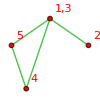
-Graphics-{35977→v13x24x5+v13x25x4+v13x2x4x5,3}Planar contraction (late)

```mathematica
CosyPrint5[alfaKey, sixNodes]
```

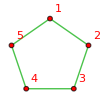
-Graphics-{20665→v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,10}Planar contraction (late)

```mathematica
CosyPrint5[lambdaKey, sixNodes]
```

```mathematica
InverseKey[colofour_,assoc_:sixNodes]:=First[Select[Keys[assoc],assoc[#]["colofour"]==colofour&]]
```

```mathematica
Table[CosyPrint5[InverseKey[k]],{k,{v13x24x5,v13x25x4,v13x2x4x5,v1x24x35,v1x24x3x5}}]
```

{-Graphics-{36166→v13x24x5,1}No IH,-Graphics-{36112→v13x25x4,1}No IH,-Graphics-{36085→v13x2x4x5,1}No IH,-Graphics-{29608→v1x24x35,1}No IH,-Graphics-{29605→v1x24x3x5,1}No IH}

```mathematica
ineqsthree52&&(2 v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5==0)//Simplify
```

False

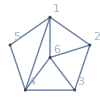
-Graphics-{B47→2 v13x24x5+v13x25x4+v13x2x4x5+v1x24x35+v1x24x3x5,6}No IH (later)

```mathematica
CosyPrint5["B47", sixNodes]
```

```mathematica
GetCompSix[key_]:=Block[{},sixNodes[key]]
```

```mathematica
SetCompSix[key_,value_]:=Block[{},sixNodes[key]=value]
```

```mathematica
CompGraph[getter_,key_]:=Labeled[Framed[Labeled[getter[key]["graph"],{Style[getter[key]["comp"],If[ToString[getter[key]["comp"]]=="Greater",Green,Red]],key},{Bottom,Top}]] ,key]
```

```mathematica
CompGraph[getter_,key_,colof_]:=Labeled[Framed[Labeled[getter[key]["graph"],{Style[getter[key]["comp"],If[ToString[getter[key]["comp"]]=="Greater",Green,Red]],getter[key][colof]},{Bottom,Top}]] ,key]
```

```mathematica
CheckCompFromRelations[getter_,setter_,key_]:=Block[{current=getter[key],rel2, lhs, rhs,one,two,three,onecomp,twocomp,threecomp, why,hold},
Table[
rel2=Simplify[rel];
lhs=rel2[[1]];
rhs=rel2[[2]];
If[Length[lhs]==0,
one=SymbolToKey[lhs];
two=SymbolToKey[rhs[[1]]];
three=SymbolToKey[rhs[[2]]];
,
one=SymbolToKey[rhs];
two=SymbolToKey[lhs[[1]]];
three=SymbolToKey[lhs[[2]]]
];
onecomp=ToString[getter[one]["comp"]];
twocomp=ToString[getter[two]["comp"]];
threecomp=ToString[getter[three]["comp"]];
If[onecomp=="GreaterEqual",
If[(twocomp=="Greater" )||( threecomp=="Greater"),
why="the relation holds : " <> ToString[rel2];
If[twocomp=="Greater",why=why <> " and x" <> ToString[two]<> " has a strictly positive colofour"];
If[threecomp=="Greater",why=why <> " and x" <> ToString[three]<> " has a strictly positive colofour"];
Print[{one,two,three,rel2,why,CompGraph[getter,one]==CompGraph[getter,two]+ CompGraph[getter,three]}];
hold=getter[one];
hold["compwhy"]=why;
hold["comp"]=Greater;
setter[one,hold];
1,
0
],
0
]
,{rel,current["relations"]}
]//Flatten
]
```

```mathematica
PropagateComp[getter_,setter_,keyset_:Keys[sixNodes]]:=Monitor[Flatten[Table[CheckCompFromRelations[getter,setter,key],{key,keyset}]],key]//Total
```

```mathematica
PropagateComp[GetCompSix,SetCompSix,Keys[sixNodes]]
```

{1066,1093,20803,x1066==x1093+x20803,the relation holds : x1066 == x1093 + x20803 and x20803 has a strictly positive colofour,-Graphics-GreaterEqual10661066==-Graphics-Greater2080320803+-Graphics-GreaterEqual10931093}

{1146,1174,23072,x1146==x1174+x23072,the relation holds : x1146 == x1174 + x23072 and x23072 has a strictly positive colofour,-Graphics-GreaterEqual11461146==-Graphics-Greater2307223072+-Graphics-GreaterEqual11741174}

{2470,36004,9031,x2470==x36004+x9031,the relation holds : x2470 == x36004 + x9031 and x36004 has a strictly positive colofour,-Graphics-GreaterEqual24702470==-Graphics-Greater3600436004+-Graphics-GreaterEqual90319031}

{2473,36736,9763,x2473==x36736+x9763,the relation holds : x2473 == x36736 + x9763 and x36736 has a strictly positive colofour,-Graphics-GreaterEqual24732473==-Graphics-Greater3673636736+-Graphics-GreaterEqual97639763}

{3172,35977,9733,x3172==x35977+x9733,the relation holds : x3172 == x35977 + x9733 and x35977 has a strictly positive colofour,-Graphics-GreaterEqual31723172==-Graphics-Greater3597735977+-Graphics-GreaterEqual97339733}

{3199,36004,9760,x3199==x36004+x9760,the relation holds : x3199 == x36004 + x9760 and x36004 has a strictly positive colofour,-Graphics-GreaterEqual31993199==-Graphics-Greater3600436004+-Graphics-GreaterEqual97609760}

{6922,26605,49204,x26605+x49204==x6922,the relation holds : x26605 + x49204 == x6922 and x49204 has a strictly positive colofour,-Graphics-GreaterEqual69226922==-Graphics-Greater4920449204+-Graphics-GreaterEqual2660526605}

{7003,28873,51472,x28873+x51472==x7003,the relation holds : x28873 + x51472 == x7003 and x51472 has a strictly positive colofour,-Graphics-GreaterEqual70037003==-Graphics-Greater5147251472+-Graphics-GreaterEqual2887328873}

{7387,27610,7657,x27610+x7657==x7387,the relation holds : x27610 + x7657 == x7387 and x27610 has a strictly positive colofour,-Graphics-GreaterEqual73877387==-Graphics-Greater2761027610+-Graphics-GreaterEqual76577657}

{7624,27307,49204,x27307+x49204==x7624,the relation holds : x27307 + x49204 == x7624 and x49204 has a strictly positive colofour,-Graphics-GreaterEqual76247624==-Graphics-Greater4920449204+-Graphics-GreaterEqual2730727307}

{7651,27334,49204,x27334+x49204==x7651,the relation holds : x27334 + x49204 == x7651 and x49204 has a strictly positive colofour,-Graphics-GreaterEqual76517651==-Graphics-Greater4920449204+-Graphics-GreaterEqual2733427334}

{7704,29574,51472,x29574+x51472==x7704,the relation holds : x29574 + x51472 == x7704 and x51472 has a strictly positive colofour,-Graphics-GreaterEqual77047704==-Graphics-Greater5147251472+-Graphics-GreaterEqual2957429574}

{7732,29602,51472,x29602+x51472==x7732,the relation holds : x29602 + x51472 == x7732 and x51472 has a strictly positive colofour,-Graphics-GreaterEqual77327732==-Graphics-Greater5147251472+-Graphics-GreaterEqual2960229602}

{9031,30172,9760,x30172+x9760==x9031,the relation holds : x30172 + x9760 == x9031 and x30172 has a strictly positive colofour,-Graphics-GreaterEqual90319031==-Graphics-Greater3017230172+-Graphics-GreaterEqual97609760}

{9109,28792,49204,x28792+x49204==x9109,the relation holds : x28792 + x49204 == x9109 and x49204 has a strictly positive colofour,-Graphics-GreaterEqual91099109==-Graphics-Greater4920449204+-Graphics-GreaterEqual2879228792}

{9811,29494,49204,x29494+x49204==x9811,the relation holds : x29494 + x49204 == x9811 and x49204 has a strictly positive colofour,-Graphics-GreaterEqual98119811==-Graphics-Greater4920449204+-Graphics-GreaterEqual2949429494}

{9838,29521,49204,x29521+x49204==x9838,the relation holds : x29521 + x49204 == x9838 and x49204 has a strictly positive colofour,-Graphics-GreaterEqual98389838==-Graphics-Greater4920449204+-Graphics-GreaterEqual2952129521}

{19780,20050,27610,x19780==x20050+x27610,the relation holds : x19780 == x20050 + x27610 and x27610 has a strictly positive colofour,-Graphics-GreaterEqual1978019780==-Graphics-Greater2761027610+-Graphics-GreaterEqual2005020050}

{20020,20047,20803,x20020==x20047+x20803,the relation holds : x20020 == x20047 + x20803 and x20803 has a strictly positive colofour,-Graphics-GreaterEqual2002020020==-Graphics-Greater2080320803+-Graphics-GreaterEqual2004720047}

{20748,20775,20803,x20748==x20775+x20803,the relation holds : x20748 == x20775 + x20803 and x20803 has a strictly positive colofour,-Graphics-GreaterEqual2074820748==-Graphics-Greater2080320803+-Graphics-GreaterEqual2077520775}

{20749,20776,20803,x20749==x20776+x20803,the relation holds : x20749 == x20776 + x20803 and x20803 has a strictly positive colofour,-Graphics-GreaterEqual2074920749==-Graphics-Greater2080320803+-Graphics-GreaterEqual2077620776}

{20775,20776,22964,x20775==x20776+x22964,the relation holds : x20775 == x20776 + x22964 and x22964 has a strictly positive colofour,-Graphics-GreaterEqual2077520775==-Graphics-Greater2296422964+-Graphics-GreaterEqual2077620776}

{21886,29176,36736,x21886==x29176+x36736,the relation holds : x21886 == x29176 + x36736 and x36736 has a strictly positive colofour,-Graphics-GreaterEqual2188621886==-Graphics-Greater3673636736+-Graphics-GreaterEqual2917629176}

{22125,28686,35976,x22125==x28686+x35976,the relation holds : x22125 == x28686 + x35976 and x35976 has a strictly positive colofour,-Graphics-GreaterEqual2212522125==-Graphics-Greater3597635976+-Graphics-GreaterEqual2868628686}

{22126,28687,35977,x22126==x28687+x35977,the relation holds : x22126 == x28687 + x35977 and x35977 has a strictly positive colofour,-Graphics-GreaterEqual2212622126==-Graphics-Greater3597735977+-Graphics-GreaterEqual2868728687}

{22152,28713,36003,x22152==x28713+x36003,the relation holds : x22152 == x28713 + x36003 and x36003 has a strictly positive colofour,-Graphics-GreaterEqual2215222152==-Graphics-Greater3600336003+-Graphics-GreaterEqual2871328713}

{22153,28714,36004,x22153==x28714+x36004,the relation holds : x22153 == x28714 + x36004 and x36004 has a strictly positive colofour,-Graphics-GreaterEqual2215322153==-Graphics-Greater3600436004+-Graphics-GreaterEqual2871428714}

{22156,29446,36736,x22156==x29446+x36736,the relation holds : x22156 == x29446 + x36736 and x36736 has a strictly positive colofour,-Graphics-GreaterEqual2215622156==-Graphics-Greater3673636736+-Graphics-GreaterEqual2944629446}

{22206,22207,22964,x22206==x22207+x22964,the relation holds : x22206 == x22207 + x22964 and x22964 has a strictly positive colofour,-Graphics-GreaterEqual2220622206==-Graphics-Greater2296422964+-Graphics-GreaterEqual2220722207}

{22233,22234,22964,x22233==x22234+x22964,the relation holds : x22233 == x22234 + x22964 and x22964 has a strictly positive colofour,-Graphics-GreaterEqual2223322233==-Graphics-Greater2296422964+-Graphics-GreaterEqual2223422234}

{22287,22315,23072,x22287==x22315+x23072,the relation holds : x22287 == x22315 + x23072 and x23072 has a strictly positive colofour,-Graphics-GreaterEqual2228722287==-Graphics-Greater2307223072+-Graphics-GreaterEqual2231522315}

{22662,22744,23072,x22662==x22744+x23072,the relation holds : x22662 == x22744 + x23072 and x23072 has a strictly positive colofour,-Graphics-GreaterEqual2266222662==-Graphics-Greater2307223072+-Graphics-GreaterEqual2274422744}

{22854,29415,35976,x22854==x29415+x35976,the relation holds : x22854 == x29415 + x35976 and x35976 has a strictly positive colofour,-Graphics-GreaterEqual2285422854==-Graphics-Greater3597635976+-Graphics-GreaterEqual2941529415}

{22855,29416,35977,x22855==x29416+x35977,the relation holds : x22855 == x29416 + x35977 and x35977 has a strictly positive colofour,-Graphics-GreaterEqual2285522855==-Graphics-Greater3597735977+-Graphics-GreaterEqual2941629416}

{22881,29442,36003,x22881==x29442+x36003,the relation holds : x22881 == x29442 + x36003 and x36003 has a strictly positive colofour,-Graphics-GreaterEqual2288122881==-Graphics-Greater3600336003+-Graphics-GreaterEqual2944229442}

{22882,29443,36004,x22882==x29443+x36004,the relation holds : x22882 == x29443 + x36004 and x36004 has a strictly positive colofour,-Graphics-GreaterEqual2288222882==-Graphics-Greater3600436004+-Graphics-GreaterEqual2944329443}

{22899,22981,23072,x22899==x22981+x23072,the relation holds : x22899 == x22981 + x23072 and x23072 has a strictly positive colofour,-Graphics-GreaterEqual2289922899==-Graphics-Greater2307223072+-Graphics-GreaterEqual2298122981}

{22908,22990,23072,x22908==x22990+x23072,the relation holds : x22908 == x22990 + x23072 and x23072 has a strictly positive colofour,-Graphics-GreaterEqual2290822908==-Graphics-Greater2307223072+-Graphics-GreaterEqual2299022990}

{22935,22936,22964,x22935==x22936+x22964,the relation holds : x22935 == x22936 + x22964 and x22964 has a strictly positive colofour,-Graphics-GreaterEqual2293522935==-Graphics-Greater2296422964+-Graphics-GreaterEqual2293622936}

{22962,22963,22964,x22962==x22963+x22964,the relation holds : x22962 == x22963 + x22964 and x22964 has a strictly positive colofour,-Graphics-GreaterEqual2296222962==-Graphics-Greater2296422964+-Graphics-GreaterEqual2296322963}

{23016,23044,23072,x23016==x23044+x23072,the relation holds : x23016 == x23044 + x23072 and x23072 has a strictly positive colofour,-Graphics-GreaterEqual2301623016==-Graphics-Greater2307223072+-Graphics-GreaterEqual2304423044}

{26578,28765,31681,x26578==x28765+x31681,the relation holds : x26578 == x28765 + x31681 and x31681 has a strictly positive colofour,-Graphics-GreaterEqual2657826578==-Graphics-Greater3168131681+-Graphics-GreaterEqual2876528765}

{26605,28792,31708,x26605==x28792+x31708,the relation holds : x26605 == x28792 + x31708 and x31708 has a strictly positive colofour,-Graphics-GreaterEqual2660526605==-Graphics-Greater3170831708+-Graphics-GreaterEqual2879228792}

{27036,27282,27610,x27036==x27282+x27610,the relation holds : x27036 == x27282 + x27610 and x27610 has a strictly positive colofour,-Graphics-GreaterEqual2703627036==-Graphics-Greater2761027610+-Graphics-GreaterEqual2728227282}

{27070,27340,27610,x27070==x27340+x27610,the relation holds : x27070 == x27340 + x27610 and x27610 has a strictly positive colofour,-Graphics-GreaterEqual2707027070==-Graphics-Greater2761027610+-Graphics-GreaterEqual2734027340}

{27109,27355,27610,x27109==x27355+x27610,the relation holds : x27109 == x27355 + x27610 and x27610 has a strictly positive colofour,-Graphics-GreaterEqual2710927109==-Graphics-Greater2761027610+-Graphics-GreaterEqual2735527355}

{27118,27364,27610,x27118==x27364+x27610,the relation holds : x27118 == x27364 + x27610 and x27610 has a strictly positive colofour,-Graphics-GreaterEqual2711827118==-Graphics-Greater2761027610+-Graphics-GreaterEqual2736427364}

{27306,29493,31681,x27306==x29493+x31681,the relation holds : x27306 == x29493 + x31681 and x31681 has a strictly positive colofour,-Graphics-GreaterEqual2730627306==-Graphics-Greater3168131681+-Graphics-GreaterEqual2949329493}

{27307,29494,31681,x27307==x29494+x31681,the relation holds : x27307 == x29494 + x31681 and x31681 has a strictly positive colofour,-Graphics-GreaterEqual2730727307==-Graphics-Greater3168131681+-Graphics-GreaterEqual2949429494}

{27333,29520,31708,x27333==x29520+x31708,the relation holds : x27333 == x29520 + x31708 and x31708 has a strictly positive colofour,-Graphics-GreaterEqual2733327333==-Graphics-Greater3170831708+-Graphics-GreaterEqual2952029520}

{27334,29521,31708,x27334==x29521+x31708,the relation holds : x27334 == x29521 + x31708 and x31708 has a strictly positive colofour,-Graphics-GreaterEqual2733427334==-Graphics-Greater3170831708+-Graphics-GreaterEqual2952129521}

{28686,29415,30172,x28686==x29415+x30172,the relation holds : x28686 == x29415 + x30172 and x30172 has a strictly positive colofour,-Graphics-GreaterEqual2868628686==-Graphics-Greater3017230172+-Graphics-GreaterEqual2941529415}

{28687,29416,30172,x28687==x29416+x30172,the relation holds : x28687 == x29416 + x30172 and x30172 has a strictly positive colofour,-Graphics-GreaterEqual2868728687==-Graphics-Greater3017230172+-Graphics-GreaterEqual2941629416}

{28713,29442,30172,x28713==x29442+x30172,the relation holds : x28713 == x29442 + x30172 and x30172 has a strictly positive colofour,-Graphics-GreaterEqual2871328713==-Graphics-Greater3017230172+-Graphics-GreaterEqual2944229442}

{28714,29443,30172,x28714==x29443+x30172,the relation holds : x28714 == x29443 + x30172 and x30172 has a strictly positive colofour,-Graphics-GreaterEqual2871428714==-Graphics-Greater3017230172+-Graphics-GreaterEqual2944329443}

{29415,29416,29417,x29415==x29416+x29417,the relation holds : x29415 == x29416 + x29417 and x29417 has a strictly positive colofour,-Graphics-GreaterEqual2941529415==-Graphics-Greater2941729417+-Graphics-GreaterEqual2941629416}

{B18,29413,full,x29413+xfull==xB18,the relation holds : x29413 + xfull == xB18 and x29413 has a strictly positive colofour,-Graphics-GreaterEqualB18B18==-Graphics-Greater2941329413+-Graphics-GreaterEqualfullfull}

{B19,20773,full,x20773+xfull==xB19,the relation holds : x20773 + xfull == xB19 and x20773 has a strictly positive colofour,-Graphics-GreaterEqualB19B19==-Graphics-Greater2077320773+-Graphics-GreaterEqualfullfull}

{B20,27229,full,x27229+xfull==xB20,the relation holds : x27229 + xfull == xB20 and x27229 has a strictly positive colofour,-Graphics-GreaterEqualB20B20==-Graphics-Greater2722927229+-Graphics-GreaterEqualfullfull}

{B21,22933,full,x22933+xfull==xB21,the relation holds : x22933 + xfull == xB21 and x22933 has a strictly positive colofour,-Graphics-GreaterEqualB21B21==-Graphics-Greater2293322933+-Graphics-GreaterEqualfullfull}

{B22,20695,full,x20695+xfull==xB22,the relation holds : x20695 + xfull == xB22 and x20695 has a strictly positive colofour,-Graphics-GreaterEqualB22B22==-Graphics-Greater2069520695+-Graphics-GreaterEqualfullfull}

{B23,B18,full,xB18+xfull==xB23,the relation holds : xB18 + xfull == xB23 and xB18 has a strictly positive colofour,-Graphics-GreaterEqualB23B23==-Graphics-GreaterB18B18+-Graphics-GreaterEqualfullfull}

{B24,B19,full,xB19+xfull==xB24,the relation holds : xB19 + xfull == xB24 and xB19 has a strictly positive colofour,-Graphics-GreaterEqualB24B24==-Graphics-GreaterB19B19+-Graphics-GreaterEqualfullfull}

{B25,B20,full,xB20+xfull==xB25,the relation holds : xB20 + xfull == xB25 and xB20 has a strictly positive colofour,-Graphics-GreaterEqualB25B25==-Graphics-GreaterB20B20+-Graphics-GreaterEqualfullfull}

{B26,B21,full,xB21+xfull==xB26,the relation holds : xB21 + xfull == xB26 and xB21 has a strictly positive colofour,-Graphics-GreaterEqualB26B26==-Graphics-GreaterB21B21+-Graphics-GreaterEqualfullfull}

{B27,B22,full,xB22+xfull==xB27,the relation holds : xB22 + xfull == xB27 and xB22 has a strictly positive colofour,-Graphics-GreaterEqualB27B27==-Graphics-GreaterB22B22+-Graphics-GreaterEqualfullfull}

66

```mathematica
PropagateComp[GetCompSix,SetCompSix,Keys[sixNodes]]
```

0

```mathematica
PropagateComp[GetCompSix,SetCompSix,Keys[sixNodes]]
```

0

```mathematica
Add a 7 th node
```

7 a Add node th

```mathematica
DefineB50[]:=Block[{base=sixNodes["B18"], newEntry},
newEntry=Association[];
newEntry["signature"]="B50";
Table[
newEntry[key]=Simplify[4*base[key]]
,{key,{"colofour","colortable"}}
];
newEntry["comp"]=base["comp"];
newEntry["matrix"]=base["matrix"];
newEntry["graph"]=VertexAdd[base["graph"],7];
newEntry["vertexsets"]=base["vertexsets"];
newEntry["vertices"]=base["vertices"];
newEntry["relations"]={};
newEntry
]
sixNodes["B50"]=DefineB50[];
sixNodes["B51"]=DefineNew["B51","B50","B18",EdgeAdd[sixNodes["B50","graph"],{1<->7}],Subtract];
sixNodes["B52"]=DefineNew["B52","B51","B18",EdgeAdd[sixNodes["B51","graph"],{2<->7}],Subtract];
sixNodes["B53"]=DefineNew["B53","B52","full",EdgeAdd[sixNodes["B52","graph"],{6<->7}],Subtract];
```

```mathematica
sixNodes["B54"]=DefineNew["B54","B53","B43",EdgeAdd[sixNodes["B53","graph"],{5<->7}],Subtract]
```

<|signature→B54,colofour→v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5,colortable→{{0,v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x25x4,v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v14x25x3,v13x25x4+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{0,v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{0,v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v1x24x35+v1x24x3x5,v13x25x4+v14x25x3+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v13x25x4+v14x25x3+2 v1x25x3x4,v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5},{0,v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5},{v1x24x35+v1x2x35x4,v13x25x4+v14x25x3+v1x24x3x5+2 v1x25x3x4+v1x2x3x4x5},{0,v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5}},comp→GreaterEqual,compwhy→No IH (later),relations→{xB54==-xB43+xB53},graph→-Graphics-|>

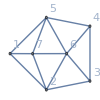
-Graphics-{B54→v13x25x4+v14x25x3+v1x24x35+v1x24x3x5+2 v1x25x3x4+v1x2x35x4+v1x2x3x4x5,7}No IH (later)

```mathematica
CosyPrint5["B54", sixNodes]
```

```mathematica
Map[CosyPrint5[InverseKey[#], treeForm5,"colofourtree"] &,ListofVars[sixNodes["B54","colofour"]]]
```

KeyExistsQ::invrl: The argument treeForm5[36112] is not a valid Association or a list of rules.

ChromaticPolynomial::graph: A graph object is expected at position 1 in ChromaticPolynomial[treeForm5[36112]["graph"], 4].

KeyExistsQ::invrl: The argument treeForm5[36112] is not a valid Association or a list of rules.

KeyExistsQ::invrl: The argument treeForm5[31738] is not a valid Association or a list of rules.

General::stop: Further output of KeyExistsQ :: invrl will be suppressed during this calculation.

ChromaticPolynomial::graph: A graph object is expected at position 1 in ChromaticPolynomial[treeForm5[31738]["graph"], 4].

ChromaticPolynomial::graph: A graph object is expected at position 1 in ChromaticPolynomial[treeForm5[29608]["graph"], 4].

General::stop: Further output of ChromaticPolynomial :: graph will be suppressed during this calculation.

{Graph[treeForm5[36112][graph],ImageSize→{100,100}]{treeForm5[36112][signature],1/24 ChromaticPolynomial[treeForm5[36112][graph],4]}treeForm5[36112][compwhy],Graph[treeForm5[31738][graph],ImageSize→{100,100}]{treeForm5[31738][signature],1/24 ChromaticPolynomial[treeForm5[31738][graph],4]}treeForm5[31738][compwhy],Graph[treeForm5[29608][graph],ImageSize→{100,100}]{treeForm5[29608][signature],1/24 ChromaticPolynomial[treeForm5[29608][graph],4]}treeForm5[29608][compwhy],Graph[treeForm5[29605][graph],ImageSize→{100,100}]{treeForm5[29605][signature],1/24 ChromaticPolynomial[treeForm5[29605][graph],4]}treeForm5[29605][compwhy],Graph[treeForm5[29527][graph],ImageSize→{100,100}]{treeForm5[29527][signature],1/24 ChromaticPolynomial[treeForm5[29527][graph],4]}treeForm5[29527][compwhy],Graph[treeForm5[29524][graph],ImageSize→{100,100}]{treeForm5[29524][signature],1/24 ChromaticPolynomial[treeForm5[29524][graph],4]}treeForm5[29524][compwhy],Graph[treeForm5[29551][graph],ImageSize→{100,100}]{treeForm5[29551][signature],1/24 ChromaticPolynomial[treeForm5[29551][graph],4]}treeForm5[29551][compwhy]}

```mathematica
CosyPrint5["B43", treeForm5,"colofourtree"]
```

KeyExistsQ::invrl: The argument treeForm5["B43"] is not a valid Association or a list of rules.

ChromaticPolynomial::graph: A graph object is expected at position 1 in ChromaticPolynomial[treeForm5["B43"]["graph"], 4].

KeyExistsQ::invrl: The argument treeForm5["B43"] is not a valid Association or a list of rules.

Graph[treeForm5[B43][graph],ImageSize→{100,100}]{treeForm5[B43][signature],1/24 ChromaticPolynomial[treeForm5[B43][graph],4]}treeForm5[B43][compwhy]

```mathematica
Map[{CompGraph[GetCompSix,InverseKey[#]],sixNodes[InverseKey[#],"comp"]}&,ListofVars[sixNodes["B43","colofour"]]]
```

{{-Graphics-GreaterEqual3616636166,GreaterEqual},{-Graphics-GreaterEqual3171431714,GreaterEqual},{-Graphics-GreaterEqual2960529605,GreaterEqual},{-Graphics-GreaterEqual2952729527,GreaterEqual},{-Graphics-GreaterEqual2960829608,GreaterEqual}}

```mathematica
sixNodes[36166]
```

<|signature→36166,matrix→{{2,1,2,1,1},{1,2,1,2,1},{2,1,2,1,1},{1,2,1,2,1},{1,1,1,1,2}},graph→-Graphics-,vertexsets→{{5},{1,3},{2,4}},vertices→{1,2,3},edges→{{1,2},{1,3},{2,3}},relations→{x36166==x35434-x36898,x36166==x36138-x36194,x36166==x14044-x58288},links→{},colofour→v13x24x5,colortable→{{0,v13x24x5},{v13x24x5,0},{0,v13x24x5},{0,v13x24x5},{0,v13x24x5},{v13x24x5,0},{0,v13x24x5},{0,v13x24x5},{0,v13x24x5},{0,v13x24x5}},colortable2→{{0,v13x24x5},{v13x24x5,0},{0,v13x24x5},{0,v13x24x5},{0,v13x24x5},{v13x24x5,0},{0,v13x24x5},{0,v13x24x5},{0,v13x24x5},{0,v13x24x5}},comp→GreaterEqual,compwhy→No IH,marked→True,parents→{36138,35434,36004,33808,36003,33807,35977,33781,23044,23041,22792,22789,22315,22063,14044,16078,16077,16051,1174,1171,445},children→{}|>

## Find the tree base

```mathematica
treeForm5=sixNodes;
```

First we get the keys of everything which is a tree.

```mathematica
treeKeys5=Select[Keys[treeForm5],With[{g=treeForm5[#,"graph"]},TreeGraphQ[g]]&];Length[treeKeys5]
```

376

Ensure that they use all the variables in their colofour

```mathematica
Flatten[Table[ListofVars[treeForm5[ k,"colofour"]],{k,treeKeys5}]]//DeleteDuplicates//Length
```

52

Now we compose a set of equations.one for each tree.  We define new variables for the trees.

```mathematica
treeEquations5=Table[Symbol["t"<>ToString[k]]==treeForm5[k,"colofour"],{k,treeKeys5}];Length[treeEquations5]
```

376

We now reduce them to the atom variables.  Since there are too many trees, some trees will be defined as a function of other trees

```mathematica
reducedTreeEquations5= Reduce[treeEquations5,baseGraphAxioma5Vars];Length[reducedTreeEquations5]
```

376

```mathematica
reducedTreeEquationsList5=Table[reducedTreeEquations5[[k]],{k,Length[reducedTreeEquations5]}];
```

we filter out equations that are “tree” only, which means they don’t contain any of the base axioms

```mathematica
reducedTreeEquationsList5Base=Select[reducedTreeEquationsList5,Intersection[ListofVars[#],baseGraphAxioma5Vars]≠{}&];Length[reducedTreeEquationsList5Base]
```

52

```mathematica
treeVars5=Select[ListofVars[reducedTreeEquationsList5Base]//DeleteDuplicates//Sort,StringStartsQ[SymbolName[#],"t"]&];Take[treeVars5,4]
```

{t29888,t3898,t39014,t3970}

```mathematica
treeKeys5=Map[SymbolToKey,treeVars5];Length[treeKeys5]
```

52

```mathematica
Table[treeForm5[k,"comp"],{k,treeKeys5}]//Tally
```

{{Greater,51},{GreaterEqual,1}}

```mathematica
Monitor[Table[MyPlanar[treeForm5,k],{k,treeKeys5}],k]//Tally
```

{{True,27},{False,25}}

Compute the matrix of the tree transformation

```mathematica
repTree5=Map[#[[1]]->#[[2]]&,reducedTreeEquationsList5Base];Take[repTree5,5]
```

{v12345→t59048,v1234x5→t58288,v1235x4→t56770,v123x45→t56012,v123x4x5→-t58288-t7380-t7480+t7614+t7704+t7738+t820+t922+t9587-t9722-t9819-t982}

```mathematica
repTreeGraphics5=Table[treeForm5[k,"colofourtree"]->Labeled[treeForm5[k,"graph"],Style[k,ColourForKey[treeForm5,k]]],{k,treeKeys5}];
```

```mathematica
matTree5=CoefficientArrays[Map[#[[2]]&,repTree5],treeVars5][[2]];
```

```mathematica
Monitor[Table[
treeForm5[k,"colofourtree"]=Simplify[(treeForm5[k,"colofour"]/.repTree5)];
treeForm5[k,"colortabletree"]=Simplify[(treeForm5[k,"colortable"]/.repTree5)]
,{k,Keys[treeForm5]}],k];
```

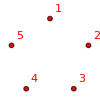
-Graphics-{0→t29888+t3898+t39014+t56012+t56770+t59048-t7480+2 t7647+t7704+3 t7738+t8112+t820+t8436+t8797-t9018-t9048+t9117+2 t9148+t922+t9587+t9720-t9722+t976-2 t9819-2 t982+t984,128/3}Since x0 == x19683 + x39366 and 19683 is Greater and 39366 is Greater

```mathematica
CosyPrint5[0,treeForm5,"colofourtree"]
```

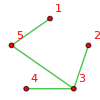
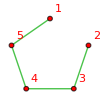
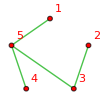
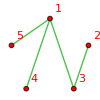
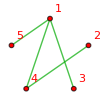
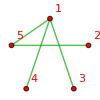
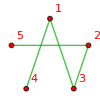
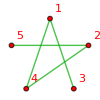
{-Graphics-{984→t984,27/2}Since x984 == x20667 + x46938 and 20667 is GreaterEqual and 46938 is Greater,-Graphics-{982→t982,27/2}Planar contraction (late),-Graphics-{976→t976,27/2}Since x976 == x20659 + x46930 and 20659 is Greater and 46930 is Greater,-Graphics-{9720→t9720,27/2}Since x9720 == x29403 + x49194 and 29403 is Greater and 49194 is Greater,-Graphics-{9558→t9558,27/2}Since x9558 == x29241 + x49194 and 29241 is Greater and 49194 is Greater,-Graphics-{9504→t9504,27/2}Since x9504 == x29187 + x49194 and 29187 is Greater and 49194 is Greater,-Graphics-{9018→t9018,27/2}Since x9018 == x28701 + x49194 and 28701 is Greater and 49194 is Greater,-Graphics-{8856→t8856,27/2}Since x8856 == x28539 + x49194 and 28539 is Greater and 49194 is Greater,-Graphics-{8778→t8778,27/2}Since x8778 == x28461 + x49197 and 28461 is Greater and 49197 is Greater,-Graphics-{846→t846,27/2}Since x846 == x20529 + x42399 and 20529 is Greater and 42399 is Greater,-Graphics-{840→t840,27/2}Since x840 == x20523 + x42393 and 20523 is Greater and 42393 is Greater,-Graphics-{822→t822,27/2}Since x822 == x20505 + x42402 and 20505 is Greater and 42402 is Greater,-Graphics-{820→t820,27/2}Since x820 == x20503 + x42400 and 20503 is Greater and 42400 is Greater,-Graphics-{814→t814,27/2}Since x814 == x20497 + x42394 and 20497 is Greater and 42394 is Greater,-Graphics-{7614→t7614,27/2}Since x7614 == x27297 + x49194 and 27297 is Greater and 49194 is Greater,-Graphics-{7398→t7398,27/2}Since x7398 == x27081 + x49194 and 27081 is Greater and 49194 is Greater,-Graphics-{7380→t7380,27/2}Since x7380 == x27063 + x49203 and 27063 is Greater and 49203 is Greater,-Graphics-{9819→t9819,9/2}Since x9819 == x29502 + x49212 and 29502 is Greater and 49212 is Greater,-Graphics-{9753→t9753,9/2}Since x9753 == x29436 + x49200 and 29436 is Greater and 49200 is Greater,-Graphics-{9722→t9722,9/2}Since x9722 == x29405 + x49196 and 29405 is Greater and 49196 is Greater,-Graphics-{9587→t9587,9/2}Since x9587 == x29270 + x49196 and 29270 is Greater and 49196 is Greater,-Graphics-{9564→t9564,9/2}Since x9564 == x29247 + x49200 and 29247 is Greater and 49200 is Greater,-Graphics-{9522→t9522,9/2}Since x9522 == x29205 + x49212 and 29205 is Greater and 49212 is Greater,-Graphics-{922→t922,9/2}Since x922 == x14044 + x7483 and 14044 is Greater and 7483 is Greater,-Graphics-{9117→t9117,9/2}Since x9117 == x28800 + x49212 and 28800 is Greater and 49212 is Greater,-Graphics-{9048→t9048,9/2}Since x9048 == x29460 + x49954 and 29460 is GreaterEqual and 49954 is Greater,-Graphics-{8884→t8884,9/2}Since x8884 == x29296 + x49954 and 29296 is GreaterEqual and 49954 is Greater,-Graphics-{8797→t8797,9/2}Since x8797 == x28480 + x49216 and 28480 is Greater and 49216 is Greater,-Graphics-{8346→t8346,9/2}Since x8346 == x28056 + x49954 and 28056 is Greater and 49954 is Greater,-Graphics-{8112→t8112,9/2}Since x8112 == x28308 + x8355 and 28308 is Greater and 8355 is Greater,-Graphics-{778→t778,9/2}Since x778 == x20461 + x40144 and 20461 is Greater and 40144 is Greater,-Graphics-{7704→t7704,9/2}the relation holds : x29574 + x51472 == x7704 and x51472 has a strictly positive colofour,-Graphics-{7647→t7647,9/2}Since x7647 == x27330 + x49200 and 27330 is Greater and 49200 is Greater,-Graphics-{7480→t7480,9/2}Since x7480 == x29350 + x51472 and 29350 is Greater and 51472 is GreaterEqual,-Graphics-{49194→t49194,9/2}Since x49194 == x49203 + x49212 and 49203 is Greater and 49212 is Greater,-Graphics-{3970→t3970,9/2}Since x3970 == x23680 + x49954 and 23680 is Greater and 49954 is Greater,-Graphics-{3898→t3898,9/2}Since x3898 == x23770 + x3979 and 23770 is GreaterEqual and 3979 is Greater,-Graphics-{9854→t9854,3/2}Since x9854 == x29537 + x49220 and 29537 is Greater and 49220 is Greater,-Graphics-{9148→t9148,3/2}Since x9148 == x29560 + x49972 and 29560 is GreaterEqual and 49972 is Greater,-Graphics-{8436→t8436,3/2}Since x8436 == x30334 + x52232 and 30334 is GreaterEqual and 52232 is Greater,-Graphics-{7738→t7738,3/2}No IH,-Graphics-{7034→t7034,3/2}Since x7034 == x29633 + x52232 and 29633 is GreaterEqual and 52232 is Greater,-Graphics-{49212→t49212,3/2}Since x49212 == x49216 + x49220 and 49216 is Greater and 49220 is Greater,-Graphics-{49200→t49200,3/2}Since x49200 == x49210 + x49220 and 49210 is GreaterEqual and 49220 is Greater,-Graphics-{49196→t49196,3/2}Since x49196 == x49208 + x49220 and 49208 is Greater and 49220 is Greater,-Graphics-{58288→t58288,1/2}Planar contraction,-Graphics-{56770→t56770,1/2}Planar contraction,-Graphics-{56012→t56012,1/2}Planar contraction,-Graphics-{49220→t49220,1/2}Planar contraction,-Graphics-{39014→t39014,1/2}Planar contraction,-Graphics-{29888→t29888,1/2}Planar contraction,-Graphics-{59048→t59048,1/6}Planar contraction}

```mathematica
Table[CosyPrint5[k,treeForm5,"colofourtree"],{k,Sort[treeKeys5,VertexCount[treeForm5[#1,"graph"]]>VertexCount[treeForm5[#2,"graph"]]&]}]
```

```mathematica
treeForm5["full","colofourtree"]/.repTreeGraphics5
```

t49194-t49196-t49200-t49212+2 t49220-t58288+t7034-t7480+2 t7647+t7738+t822-t8436-t846+t8778-t8797-t8856+t8884-t9048+t9117+t922-t9564-t9720+t9722+2 t9753+t9819-4 t9854

```mathematica
Select[Keys[treeForm5],IsomorphicGraphQ[treeForm5[#]["graph"],CompleteGraph[5]]&]
```

{29524}

```mathematica
Simplify[treeForm5[k5Key,"colofourtree"]==0]/.repTreeGraphics5
```

t49194+2 t49220+4 t58288+2 t7034+4 t7480+4 t7647+4 t840+2 t8778+2 t9048+2 t9117+t9522+t9558+t9564+t9722+2 t9753==t49196+t49200+t49212+4 t7704+4 t778+2 t8436+4 t846+2 t8797+2 t8856+2 t8884+t9504+t9720+8 t9854

```mathematica
Reduce[treeForm5[k5Key,"colofourtree"]==0,t49194]
```

t49194==t49196+t49200+t49212-2 t49220-4 t58288-2 t7034-4 t7480-4 t7647+4 t7704+4 t778-4 t840+2 t8436+4 t846-2 t8778+2 t8797+2 t8856+2 t8884-2 t9048-2 t9117+t9504-t9522-t9558-t9564+t9720-t9722-2 t9753+8 t9854

```mathematica
Simplify[treeForm5[alfa1Key,"colofourtree"]==0]/.repTreeGraphics5
```

t58288+t7480==t7738+t922

```mathematica
Simplify[treeForm5[beta1Key,"colofourtree"]==0]/.repTreeGraphics5
```

t58288+t7034+t7398+2 t7480+t7647+t7738+t820+t840+t8778+t9048+t9117+t9558+t9753+t976==t7380+2 t7704+t778+t814+t8436+t846+t8797+t8856+t8884+t9504+t9819+t982+2 t9854

```mathematica
Simplify[treeForm5["full","colofourtree"]==0]/.repTreeGraphics5
```

t49194+2 t49220+t7034+2 t7647+t7738+t822+t8778+t8884+t9117+t922+t9722+2 t9753+t9819==t49196+t49200+t49212+t58288+t7480+t8436+t846+t8797+t8856+t9048+t9564+t9720+4 t9854

```mathematica
Simplify[treeForm5[k5Key,"colofourtree"]-treeForm5["full","colofourtree"]==0]/.repTreeGraphics5
```

2 t49194+4 t49220+3 t58288+3 t7034+3 t7480+6 t7647+t7738+t822+4 t840+3 t8778+t9048+3 t9117+t922+t9522+t9558+2 t9722+4 t9753+t9819==2 t49196+2 t49200+2 t49212+4 t7704+4 t778+3 t8436+5 t846+3 t8797+3 t8856+t8884+t9504+2 t9720+12 t9854

```mathematica
stubbornKeys5 = Select[Keys[treeForm5],(ToString[treeForm5[#]["comp"]]=="GreaterEqual")&];Length[treeForm5];Length[stubbornKeys5]
```

146

```mathematica
ineqsthree5tree=Monitor[Table[treeForm5[k]["comp"][treeForm5[k]["colofourtree"],0],{k,Keys[treeForm5]}],k]//DeleteDuplicates;Length[ineqsthree5tree]
```

1916

```mathematica
ineqsthree5tree2=Simplify[Fold[And,ineqsthree5tree]&&(treeForm5[alfa1Key]["colofourtree"]==0)&&(treeForm5[beta1Key]["colofourtree"]==0)&&(treeForm5[gamma1Key]["colofourtree"]==0)&&(treeForm5[delta1Key]["colofourtree"]==0)&&(treeForm5[epsilon1Key]["colofourtree"]==0)];
```